```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*) 
mpDPointshigh = mpDPoints[[4;;]];
mpDPointslow = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-3,-2}];(*1 MeV is lowest mass given constraints on ϵ and the fact that we are scanning over meD <= 10^-2 mpD. So at 10 MeV,we run into the red giant cooling bound (since the mass of the lightest species must be above 0.1 MeV)*)


mpDPointshigher = Table["mpD"->10^i 10^12("JpereV")/("c")^2/.SIConstRepl,{i,1,3}];

mpDPointslower = Table["mpD"->10^i 10^6("JpereV")/("c")^2/.SIConstRepl,{i,-2,-1}]; 
(*These values of mpD are ruled out for by stellar cooling bounds, but are the lowest valued meD can be that is consistent with them, hence these values will be used to show capture and evaporation rates for the dark electrons *)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

#### fD

```mathematica
fDpoints = Table[10^i,{i,-3,-1}];
```

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### Debug

#### test runs

Pre branch cut fix

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
SaveIt[NotebookDirectory[]<>"FeσDicteallmasses",FeσDicteallmasses]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-734.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.697] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.694] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

40153.9 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

4192.01 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

28426.8 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

20124.6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1.70538×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

5.41386×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

12697.8 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1325.63 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

8989.33 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

6363.96 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

539287. 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

1.71201×10^6 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

4015.39 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

419.201 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

2842.68 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

2012.46 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

170538. 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

11

541386. 6.×10^7

6.×10^7

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteallmasses.dat

```mathematica
FeσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigh]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighmasses",FeσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {34.9086}. NIntegrate obtained 4.40938×10^-16 and 4.75294×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {31.3032}. NIntegrate obtained 2.6296×10^-16 and 4.95046×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {36.549}. NIntegrate obtained 1.91727×10^-16 and 6.06913×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-788.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.883] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1066.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1269.78 6.×10^7

809807.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

132.563 6.×10^7

327989.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

898.933 6.×10^7

705313.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

636.396 6.×10^7

614302.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

53928.7 6.×10^7

891975.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

4

171201. 6.×10^7

992888.

Interpolation::inhr: Requested order is too high; order has been reduced to {3,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

401.539 6.×10^7

510954.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

41.9201 6.×10^7

853950.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

284.268 6.×10^7

445022.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

201.246 6.×10^7

387598.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

17053.8 6.×10^7

447046.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

54138.6 6.×10^7

894056.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighmasses.dat

Post branch cut fix

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`k near {EnergyLoss`Private`k} = {2.91113×10^10}. NIntegrate obtained 4.85329×10^7 and 75.7821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`k near {EnergyLoss`Private`k} = {2.91157×10^10}. NIntegrate obtained 4.85109×10^7 and 67.5654 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`k near {EnergyLoss`Private`k} = {2.91267×10^10}. NIntegrate obtained 4.84553×10^7 and 78.0975 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

InterpolatingFunction[…]

8.23171

σ interpolation done

dEdlf interpolation done

11

40153.9 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

InterpolatingFunction[…]

7.65114

σ interpolation done

dEdlf interpolation done

11

4192.01 6.×10^7

6.×10^7

σ of ξ interpolation done

dσ interpolation done

InterpolatingFunction[…]

8.33912

σ interpolation done

dEdlf interpolation done

11

28426.8 6.×10^7

6.×10^7

σ of ξ interpolation done

$Aborted

```mathematica
2 "qF"/.FeTotalparams
```

{2.90783×10^10,3.56657×10^10,4.68583×10^10,9.09749×10^10,4.61514×10^11,2.11611×10^12}

The singularity still seems to be around z=1

```mathematica
Clear[StructureFunction]
```

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00320488}. NIntegrate obtained 0.0000387365 and 1.08278×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000917172}. NIntegrate obtained 3.38918×10^-6 and 1.81503×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000380795}. NIntegrate obtained 2.20065×10^-7 and 3.31279×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

$Aborted

```mathematica
Clear[zIntegraldσdER1oscillator]
```

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00320488}. NIntegrate obtained 0.0000387365 and 1.08278×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000917172}. NIntegrate obtained 3.38918×10^-6 and 1.81503×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000380795}. NIntegrate obtained 2.20065×10^-7 and 3.31279×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

$Aborted

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00698859}. NIntegrate obtained 5.12731×10^11 and 1.67911×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0343884}. NIntegrate obtained 4.54875×10^9 and 29819.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.034383}. NIntegrate obtained 2.1466×10^8 and 1151.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

$Aborted

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
FeσDictetest=AbsoluteTiming@Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,1}],m]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
FeσDicteallmasses=AbsoluteTiming@Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
FeσDicteallmasses=AbsoluteTiming@Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
Length[FeTotalparams]
```

6

#### Plots of dielectrics

```mathematica
AbsoluteTiming@Table[ϵM[u,z,"νi"]/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]
```

{0.0366597,{1+(((0.+1.75116×10^16 ⅈ)+u) (1/z^3(0.+0.103495 ⅈ) (-1/2 (3.06657×10^32-(u-z)^2) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1/2 (3.06657×10^32-(u+z)^2) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-8.75581×10^15 (-u+z) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+8.75581×10^15 (-u-z) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])+1/z^3 0.103495 (2 z-1.75116×10^16 (u-z) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1.75116×10^16 (u+z) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-1/4 (3.06657×10^32-(u-z)^2) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+1/4 (3.06657×10^32-(u+z)^2) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+4.23008×10^16 ⅈ) z^2 (1/z^3(0.+0.103495 ⅈ) (-1/2 (3.06657×10^32-(u-z)^2) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1/2 (3.06657×10^32-(u+z)^2) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-8.75581×10^15 (-u+z) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+8.75581×10^15 (-u-z) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)])+1/z^3 0.103495 (2 z-1.75116×10^16 (u-z) (-ArcTan[5.7105×10^-17 (1+u-z)]-ArcTan[5.7105×10^-17 (1-u+z)])+1.75116×10^16 (u+z) (-ArcTan[5.7105×10^-17 (1-u-z)]-ArcTan[5.7105×10^-17 (1+u+z)])-1/4 (3.06657×10^32-(u-z)^2) Log[(3.06657×10^32+(1+u-z)^2)/(3.06657×10^32+(1-u+z)^2)]+1/4 (3.06657×10^32-(u+z)^2) Log[(3.06657×10^32+(1+u+z)^2)/(3.06657×10^32+(1-u-z)^2)]))),1+(((0.+8.99966×10^15 ⅈ)+u) (1/z^3(0.+0.0843793 ⅈ) (-1/2 (8.09939×10^31-(u-z)^2) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+1/2 (8.09939×10^31-(u+z)^2) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-4.49983×10^15 (-u+z) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+4.49983×10^15 (-u-z) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])+1/z^3 0.0843793 (2 z-8.99966×10^15 (u-z) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+8.99966×10^15 (u+z) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-1/4 (8.09939×10^31-(u-z)^2) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+1/4 (8.09939×10^31-(u+z)^2) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+2.66643×10^16 ⅈ) z^2 (1/z^3(0.+0.0843793 ⅈ) (-1/2 (8.09939×10^31-(u-z)^2) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+1/2 (8.09939×10^31-(u+z)^2) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-4.49983×10^15 (-u+z) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+4.49983×10^15 (-u-z) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)])+1/z^3 0.0843793 (2 z-8.99966×10^15 (u-z) (-ArcTan[1.11115×10^-16 (1+u-z)]-ArcTan[1.11115×10^-16 (1-u+z)])+8.99966×10^15 (u+z) (-ArcTan[1.11115×10^-16 (1-u-z)]-ArcTan[1.11115×10^-16 (1+u+z)])-1/4 (8.09939×10^31-(u-z)^2) Log[(8.09939×10^31+(1+u-z)^2)/(8.09939×10^31+(1-u+z)^2)]+1/4 (8.09939×10^31-(u+z)^2) Log[(8.09939×10^31+(1+u+z)^2)/(8.09939×10^31+(1-u-z)^2)]))),1+(((0.+2.01886×10^16 ⅈ)+u) (1/z^3(0.+0.0642244 ⅈ) (-1/2 (4.07581×10^32-(u-z)^2) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+1/2 (4.07581×10^32-(u+z)^2) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1.00943×10^16 (-u+z) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1.00943×10^16 (-u-z) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])+1/z^3 0.0642244 (2 z-2.01886×10^16 (u-z) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+2.01886×10^16 (u+z) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1/4 (4.07581×10^32-(u-z)^2) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1/4 (4.07581×10^32-(u+z)^2) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+7.85863×10^16 ⅈ) z^2 (1/z^3(0.+0.0642244 ⅈ) (-1/2 (4.07581×10^32-(u-z)^2) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+1/2 (4.07581×10^32-(u+z)^2) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1.00943×10^16 (-u+z) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1.00943×10^16 (-u-z) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)])+1/z^3 0.0642244 (2 z-2.01886×10^16 (u-z) (-ArcTan[4.95328×10^-17 (1+u-z)]-ArcTan[4.95328×10^-17 (1-u+z)])+2.01886×10^16 (u+z) (-ArcTan[4.95328×10^-17 (1-u-z)]-ArcTan[4.95328×10^-17 (1+u+z)])-1/4 (4.07581×10^32-(u-z)^2) Log[(4.07581×10^32+(1+u-z)^2)/(4.07581×10^32+(1-u+z)^2)]+1/4 (4.07581×10^32-(u+z)^2) Log[(4.07581×10^32+(1+u+z)^2)/(4.07581×10^32+(1-u-z)^2)]))),1+(((0.+9.30837×10^16 ⅈ)+u) (1/z^3(0.+0.03308 ⅈ) (-1/2 (8.66457×10^33-(u-z)^2) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+1/2 (8.66457×10^33-(u+z)^2) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-4.65418×10^16 (-u+z) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+4.65418×10^16 (-u-z) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])+1/z^3 0.03308 (2 z-9.30837×10^16 (u-z) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+9.30837×10^16 (u+z) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-1/4 (8.66457×10^33-(u-z)^2) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+1/4 (8.66457×10^33-(u+z)^2) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+7.03474×10^17 ⅈ) z^2 (1/z^3(0.+0.03308 ⅈ) (-1/2 (8.66457×10^33-(u-z)^2) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+1/2 (8.66457×10^33-(u+z)^2) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-4.65418×10^16 (-u+z) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+4.65418×10^16 (-u-z) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)])+1/z^3 0.03308 (2 z-9.30837×10^16 (u-z) (-ArcTan[1.0743×10^-17 (1+u-z)]-ArcTan[1.0743×10^-17 (1-u+z)])+9.30837×10^16 (u+z) (-ArcTan[1.0743×10^-17 (1-u-z)]-ArcTan[1.0743×10^-17 (1+u+z)])-1/4 (8.66457×10^33-(u-z)^2) Log[(8.66457×10^33+(1+u-z)^2)/(8.66457×10^33+(1-u+z)^2)]+1/4 (8.66457×10^33-(u+z)^2) Log[(8.66457×10^33+(1+u+z)^2)/(8.66457×10^33+(1-u-z)^2)]))),1+(((0.+7.408×10^17 ⅈ)+u) (1/z^3(0.+0.00652082 ⅈ) (-1/2 (5.48784×10^35-(u-z)^2) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+1/2 (5.48784×10^35-(u+z)^2) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-3.704×10^17 (-u+z) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+3.704×10^17 (-u-z) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])+1/z^3 0.00652082 (2 z-7.408×10^17 (u-z) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+7.408×10^17 (u+z) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-1/4 (5.48784×10^35-(u-z)^2) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+1/4 (5.48784×10^35-(u+z)^2) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+2.84013×10^19 ⅈ) z^2 (1/z^3(0.+0.00652082 ⅈ) (-1/2 (5.48784×10^35-(u-z)^2) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+1/2 (5.48784×10^35-(u+z)^2) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-3.704×10^17 (-u+z) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+3.704×10^17 (-u-z) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)])+1/z^3 0.00652082 (2 z-7.408×10^17 (u-z) (-ArcTan[1.34989×10^-18 (1+u-z)]-ArcTan[1.34989×10^-18 (1-u+z)])+7.408×10^17 (u+z) (-ArcTan[1.34989×10^-18 (1-u-z)]-ArcTan[1.34989×10^-18 (1+u+z)])-1/4 (5.48784×10^35-(u-z)^2) Log[(5.48784×10^35+(1+u-z)^2)/(5.48784×10^35+(1-u+z)^2)]+1/4 (5.48784×10^35-(u+z)^2) Log[(5.48784×10^35+(1+u+z)^2)/(5.48784×10^35+(1-u-z)^2)]))),1+(((0.+5.21962×10^18 ⅈ)+u) (1/z^3(0.+0.00142216 ⅈ) (-1/2 (2.72444×10^37-(u-z)^2) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+1/2 (2.72444×10^37-(u+z)^2) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-2.60981×10^18 (-u+z) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+2.60981×10^18 (-u-z) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])+1/z^3 0.00142216 (2 z-5.21962×10^18 (u-z) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+5.21962×10^18 (u+z) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-1/4 (2.72444×10^37-(u-z)^2) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+1/4 (2.72444×10^37-(u+z)^2) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])))/(u+1/(1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z))(0.+9.17551×10^20 ⅈ) z^2 (1/z^3(0.+0.00142216 ⅈ) (-1/2 (2.72444×10^37-(u-z)^2) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+1/2 (2.72444×10^37-(u+z)^2) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-2.60981×10^18 (-u+z) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+2.60981×10^18 (-u-z) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])+1/z^3 0.00142216 (2 z-5.21962×10^18 (u-z) (-ArcTan[1.91585×10^-19 (1+u-z)]-ArcTan[1.91585×10^-19 (1-u+z)])+5.21962×10^18 (u+z) (-ArcTan[1.91585×10^-19 (1-u-z)]-ArcTan[1.91585×10^-19 (1+u+z)])-1/4 (2.72444×10^37-(u-z)^2) Log[(2.72444×10^37+(1+u-z)^2)/(2.72444×10^37+(1-u+z)^2)]+1/4 (2.72444×10^37-(u+z)^2) Log[(2.72444×10^37+(1+u+z)^2)/(2.72444×10^37+(1-u-z)^2)])))}}

```mathematica
uνFit[z_] := ("νi"/(2 "vF" "qF" z)) (*u ν*)
zb[sign_,ω_,mχ_,vχ_,params_]:= ((mχ vχ + <|"+"->1,"-"->(-1)|>[[sign]] Sqrt[2 mχ (1/2 mχ vχ^2 - ω "ℏ")])/(2"qF""ℏ")) /.params (*section 10.2 of notes*)
(*kb[sign_,ω_,mχ_,vχ_,params_]:= 2 ("qF"/.params)zb[sign,ω,mχ,vχ,params]*)
Thetab[ω_,k_,mχ_,vχ_,params_]:=HeavisideTheta[kb["+",ω,mχ,vχ,params]-k]HeavisideTheta[k-kb["-",ω,mχ,vχ,params]]HeavisideTheta[1/2 mχ vχ^2 - ω "ℏ"/.params]
TotalThetab[ω_,k_,mχ_,vχ_,params_]:=Sum[Thetab[ω,k,mχ,vχ,params[[i]]],{i,Length[params]}]
```

```mathematica
Clear[StructureFunction]
StructureFunction[ω_,k_,mχ_,vχ_,params_,n_:4,truncate_:True,cut_:4]:=Sum[(2 ("e")^2/(vχ "ℏ" (2 π)^2 "ϵ0") (1+HeavisideTheta[cut - "β" "ℏ" ω](1/(1-E^(- "β" "ℏ" ω))-1))/.params[[i]])(z^n/z /.z->k/(2 "qF")/.params[[i]])If[truncate,Thetab[ω,k,mχ,vχ,params[[i]]],1]Im[-("Ai"/.params[[i]]) / Dielectrics`ϵMNum[("ℏ"ω)/(2"EF"z)/.z->k/(2 "qF")/.params[[i]], k/(2 "qF")/.params[[i]], uνFit[z]/.z-> k/(2 "qF")/. params[[i]], params[[i]]]],{i,Length[params]}](*taking κ = 1*)
```

```mathematica
Clear[StructureFunctionDebug]
StructureFunctionDebug[ω_,k_,mχ_,vχ_,params_, cut_:4]:=N[Sum[Im[-("Ai"/.params[[i]]) / Dielectrics`ϵMNum[("ℏ"ω)/(2"EF"z)/.z->k/(2 "qF")/.params[[i]], k/(2 "qF")/.params[[i]], uνFit[z]/.z-> k/(2 "qF")/. params[[i]], params[[i]]]],{i,Length[params]}],30]
```

```mathematica
AbsoluteTiming@StructureFunction[10^16,10^10,"m"/.SIConstRepl,10^5,FeTotalparams]
```

{0.008336,1.65789}

```mathematica
Thetab[w 10^12,k 10^10,"m"/.SIConstRepl,10^5,FeTotalparams[[1]]]
```

HeavisideTheta[10000000000 k-9.47867×10^33 (9.11×10^-26-1.34981×10^-15 √(4.555×10^-21-1.055×10^-22 w))] HeavisideTheta[-10000000000 k+9.47867×10^33 (9.11×10^-26+1.34981×10^-15 √(4.555×10^-21-1.055×10^-22 w))]

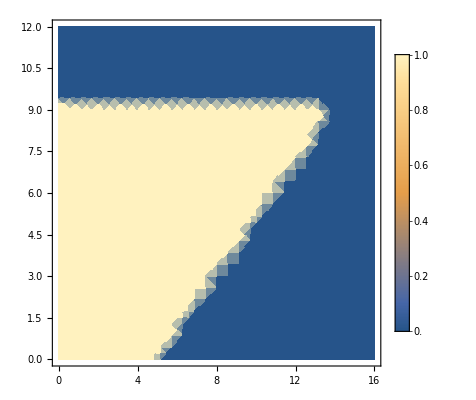

```mathematica
DensityPlot[Thetab[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams[[1]]],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

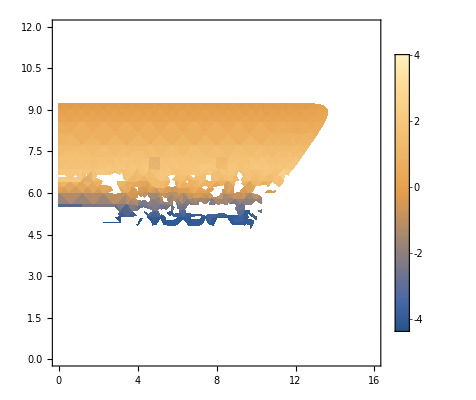

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

So the structure function becomes negative,

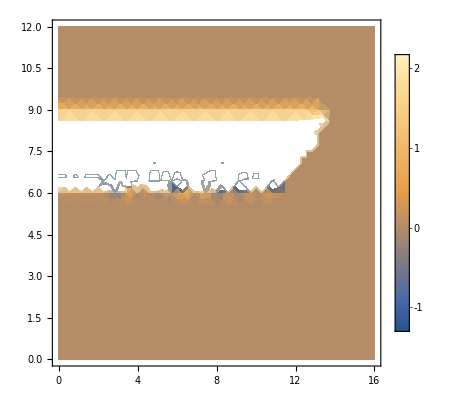

```mathematica
DensityPlot[StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

```mathematica
"qF"/.FeTotalparams
```

{1.45392×10^10,1.78329×10^10,2.34292×10^10,4.54874×10^10,2.30757×10^11,1.05805×10^12}

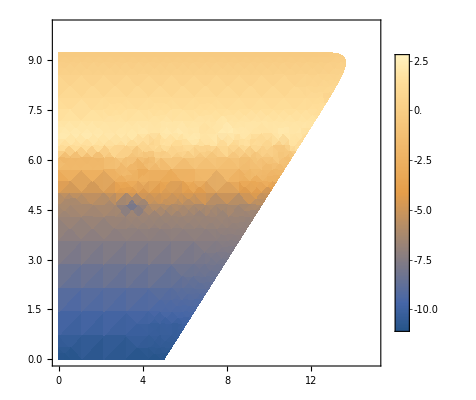

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

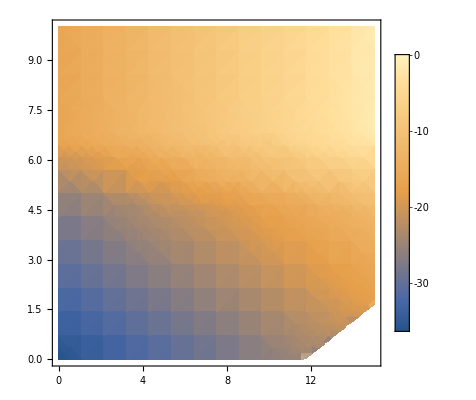

```mathematica
DensityPlot[Log10@Abs@StructureFunctionDebug[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

Here is just the imaginary part of the polarization with no kinematic restrictions, note the small scaling, it seems like there may be some differences and sums of large or small numbers where we see the grainy regions in the middle of the plot

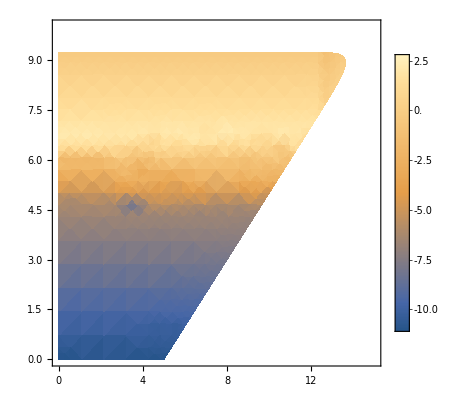

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,0.1],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

This is the same as two plots above just changing when we truncate the FD distribution (approximate as 1) - controlled by the “cut” parameter in the function. Note the top right of the plot, there is a discontinuity which reduces the value of the function slightly. This also tells us that our default cut at 4 doesn’t significantly affect the value of the function

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,100],{w,0,15},{k,0,10},PlotLegends->Automatic]
```

-Graphics-

Weaker cut still, is identical to the plot with cut = 4

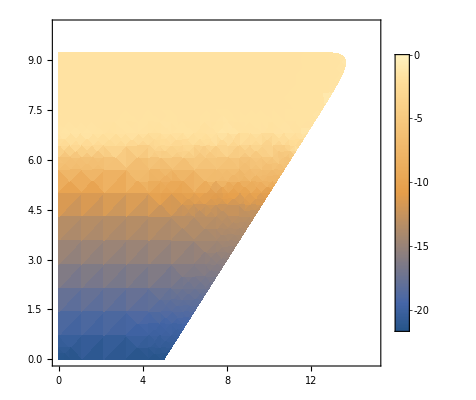

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*1st moment*)
```

Graininess reduced when we use the first moment instead of the 0th (ie. 1/small number may be responsible for the graniness). Let’s see how far we can smooth it out by working with higher moments and dividing them out after interpolating.

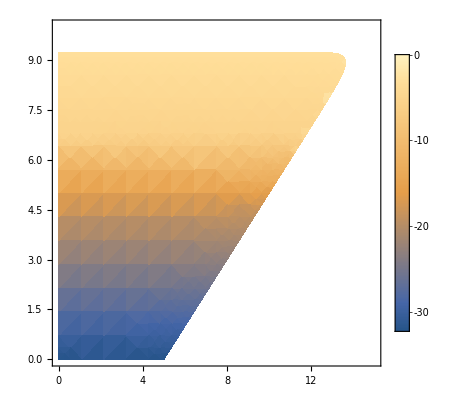

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*2nd moment*)
```

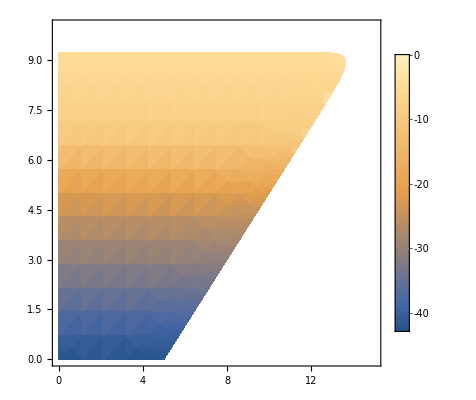

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,3],{w,0,15},{k,0,10},PlotLegends->Automatic](*3rd moment*)
```

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*3rd moment no abs*)
```

$Aborted

So the graininess / negative values are not due to the large prefactor, they just help the precision to keep it homogeneous. This seems to support the difference of large numbers hypothesis.

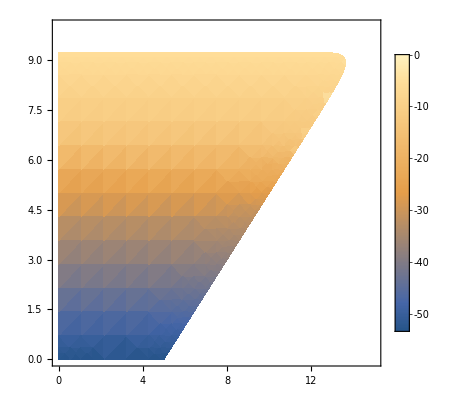

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,15},{k,0,10},PlotLegends->Automatic](*4th moment*)
```

Ooh la la so smooth. Let’s use this!

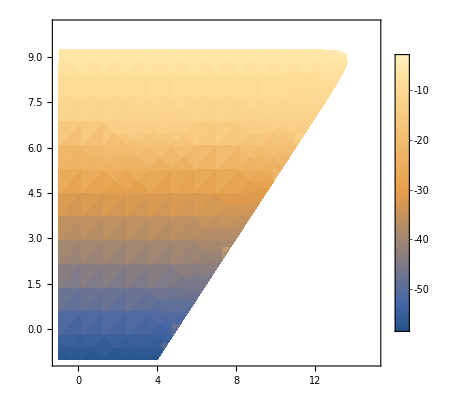

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,-1,15},{k,-1,10},PlotLegends->Automatic](*4th moment*)
```

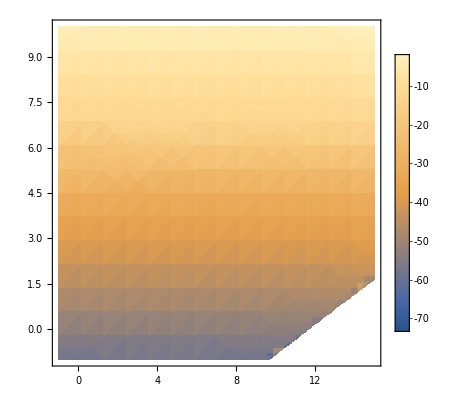

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams,4,False],{w,-1,15},{k,-1,10},PlotLegends->Automatic](*4th moment no truncation*)
```

It would be easier to use the unkinematically restricted version of the function for the interpolation since we will be using it for a range of velocities. So what is going on in the bottom right?

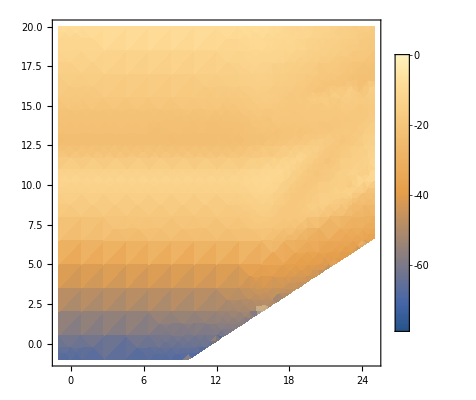

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,-1,20},PlotLegends->Automatic,PlotRange->All](*4th moment no truncation*)
```

So it looks like this may be part of the reason we are having slow down issues. Intedeterminate values may be throwing things off. Let’s look in the text files as david suggested.

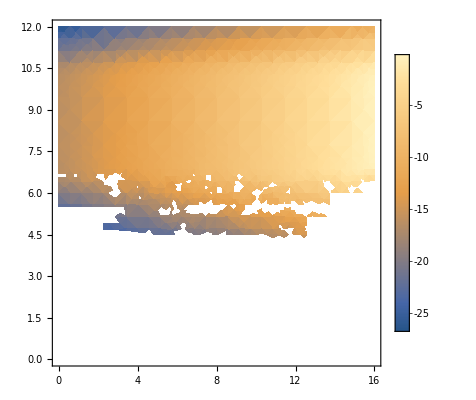

```mathematica
DensityPlot[Log10@StructureFunctionDebug[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

```mathematica
"ℏ"("qF")/("m")/.FeTotalparams
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams]/.w->1/.k->1
```

-1.09188×10^-10

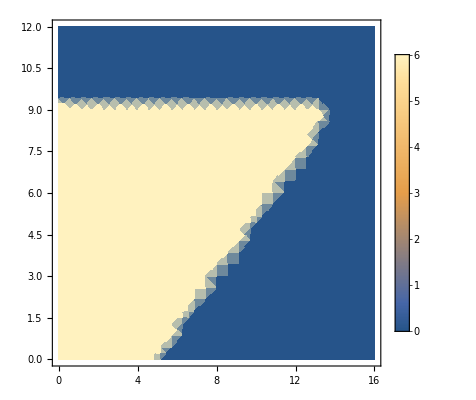

```mathematica
DensityPlot[TotalThetab[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

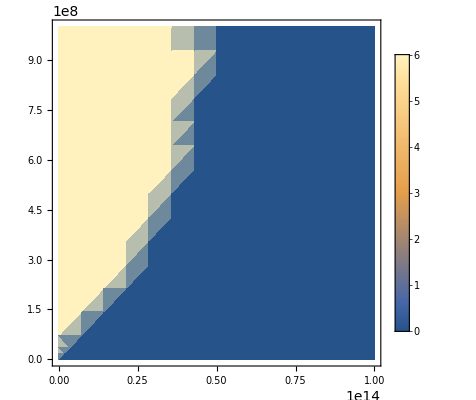

```mathematica
DensityPlot[TotalThetab[w,k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,10^14},{k,0,10^9},PlotLegends->Automatic]
```

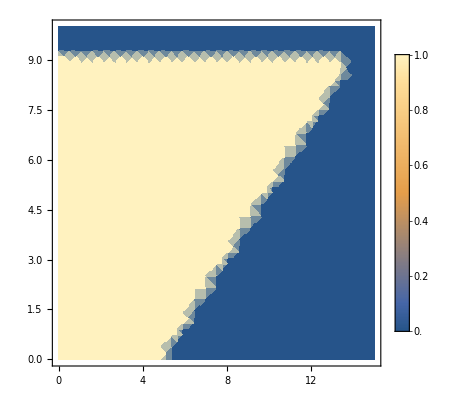

```mathematica
DensityPlot[HeavisideTheta[((10^k v-("ℏ"(10^k)^2)/(2 m))/.{m->"m"/.SIConstRepl,v->10^5}/.SIConstRepl)-10^w],{w,0,15},{k,0,10},PlotLegends->Automatic](*This is equivalent to θb*)
```

Need to interpolate, so we need to use this simpler form to change the boundaries to a rectangular grid

```mathematica
DensityPlot[kinTheta[10^k,10^w,v,m]/.{m->"m"/.SIConstRepl,v->10^5},{w,0,15},{k,0,10},PlotLegends->Automatic]
```

-Graphics-

```mathematica
{10^k,10^w}/.{m->"m"/.SIConstRepl,v->10^5}
```

{10^k,10^w}

#### Investigate z=1 pole

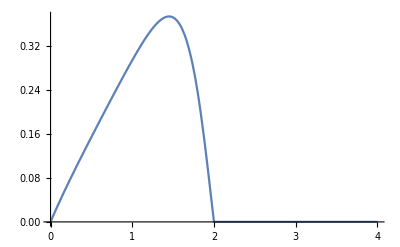

```mathematica
Plot[Im[-1/uzLinDielectric[u,1]/."χ"->1],{u,0,4}]
```

```mathematica
Plot[Im[-1/ϵM[u,1]/."χ"->1],{u,0,4}]
```

-Graphics-

```mathematica
Im[-1/ϵM[u,1,2]/."χ"->1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

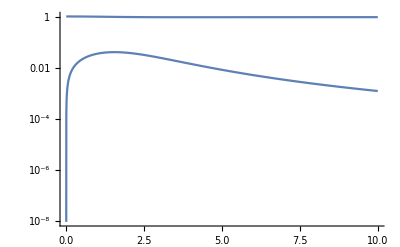

```mathematica
LogPlot[ϵRPAC[u,1,2]/."χ"->1,{u,0,10}]
```

Just complex part looks okay. Non-zero and non-singular away from 0

```mathematica
ϵM[u,z,uν]==1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))//HoldForm
```

ϵM[u,z,uν]==1+((up+ⅈ uν) ({1,ⅈ}.ϵRPAC[up,z,uν]-1))/(up+(ⅈ uν ({1,ⅈ}.ϵRPAC[up,z,uν]-1))/(ϵRPA0[z]-1))

```mathematica
ϵRPA0[z]-1
%/.z->1
```

(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
uzLinDielectric[0,z]
```

1+(χ^2 (1/2+((1-z^2) Log[Abs[(1+z)/(1-z)]])/(4 z)+ⅈ (Piecewise[{{0, z<1}, {(π (1-z^2))/(8 z), Abs[z]<1<z}, {0, True}}])))/z^2

```mathematica
Refine[uzLinDielectric[0,z],Assumptions->z>0]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

```mathematica
Limit[ϵRPA0[z]-1,z->0]
```

χ^2 ∞

```mathematica
Series[ϵRPA0[z]-1,{z,1,1}]//Simplify
```

Log[(2+(z-1)+O[z-1]^2)/Abs[1-z]] (-1/2 χ^2 (z-1)+O[z-1]^2)+(χ^2/2-χ^2 (z-1)+O[z-1]^2)

```mathematica
Series[Log[1/x],{x,0,2}]
```

Log[1/x]+O[x]^3

```mathematica
ϵM[1,1.000000000000001,1]
```

1-(0.0120658-0.222051 ⅈ) χ^2

```mathematica
Limit[ϵM[u,z,uν],z->1]
```

1+(χ^2 (8+4 (-1+u) uν (ArcTan[(2-u)/uν]+ArcTan[u/uν])+4 (1+u) uν (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-2 u+u^2-uν^2) Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(2 u+u^2-uν^2) Log[((2+u)^2+uν^2)/(u^2+uν^2)]+2 ⅈ (-((-2 u+u^2-uν^2) (ArcTan[(2-u)/uν]+ArcTan[u/uν]))+(-2 u-u^2+uν^2) (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-1+u) uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(1+u) uν Log[((2+u)^2+uν^2)/(u^2+uν^2)])))/(2 (8+2 (-2+u+ⅈ uν) uν ArcTan[(2-u)/uν]+4 (u+ⅈ uν) uν ArcTan[u/uν]-4 uν ArcTan[(2+u)/uν]-2 u uν ArcTan[(2+u)/uν]-2 ⅈ uν^2 ArcTan[(2+u)/uν]-2 ⅈ uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]+ⅈ u uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-uν^2 Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-2 ⅈ uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]-ⅈ u uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]+uν^2 Log[((2+u)^2+uν^2)/(u^2+uν^2)]))

```mathematica
1+(("χ")^2 (8+4 (-1+u) uν (ArcTan[(2-u)/uν]+ArcTan[u/uν])+4 (1+u) uν (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-2 u+u^2-uν^2) Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(2 u+u^2-uν^2) Log[((2+u)^2+uν^2)/(u^2+uν^2)]+2 ⅈ (-((-2 u+u^2-uν^2) (ArcTan[(2-u)/uν]+ArcTan[u/uν]))+(-2 u-u^2+uν^2) (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-1+u) uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-(1+u) uν Log[((2+u)^2+uν^2)/(u^2+uν^2)])))/(2 (8+2 (-2+u+ⅈ uν) uν ArcTan[(2-u)/uν]+4 (u+ⅈ uν) uν ArcTan[u/uν]-4 uν ArcTan[(2+u)/uν]-2 u uν ArcTan[(2+u)/uν]-2 ⅈ uν^2 ArcTan[(2+u)/uν]-2 ⅈ uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]+ⅈ u uν Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-uν^2 Log[(u^2+uν^2)/(4-4 u+u^2+uν^2)]-2 ⅈ uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]-ⅈ u uν Log[((2+u)^2+uν^2)/(u^2+uν^2)]+uν^2 Log[((2+u)^2+uν^2)/(u^2+uν^2)]))//FullSimplify
```

1+1/2 χ^2 (1-(ⅈ u (1+8/(-8+2 (-2+u+ⅈ uν) uν ArcTan[(-2+u)/uν]-4 (u+ⅈ uν) uν ArcTan[u/uν]+uν (2 (2+u+ⅈ uν) ArcTan[(2+u)/uν]+(2 ⅈ-ⅈ u+uν) Log[(u^2+uν^2)/((-2+u)^2+uν^2)]+ⅈ (2+u+ⅈ uν) Log[1+(4 (1+u))/(u^2+uν^2)]))))/uν)

So it has a well defined limit at the branch point.

```mathematica
N@ϵM[1,1,1]
```

1.-(0.0120658-0.222051 ⅈ) χ^2

Gang gang, all fixed

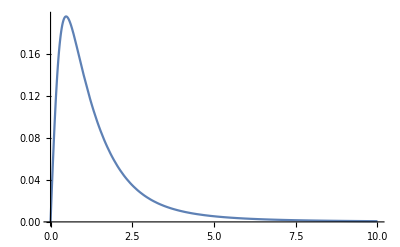

```mathematica
Plot[Im[-1/ϵM[u,1,2]/."χ"->1],{u,0,10}]
```

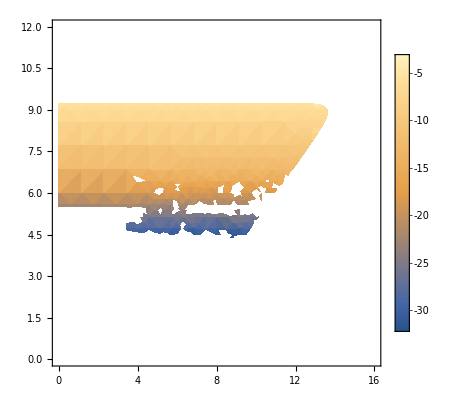

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^5,FeTotalparams],{w,0,16},{k,0,12},PlotLegends->Automatic]
```

```mathematica
Limit[ϵM[u,z,uν],z->1]//FullSimplify
```

1+1/2 χ^2 (1-(ⅈ u (1+8/(-8+2 (-2+u+ⅈ uν) uν ArcTan[(-2+u)/uν]-4 (u+ⅈ uν) uν ArcTan[u/uν]+uν (2 (2+u+ⅈ uν) ArcTan[(2+u)/uν]+(2 ⅈ-ⅈ u+uν) Log[(u^2+uν^2)/((-2+u)^2+uν^2)]+ⅈ (2+u+ⅈ uν) Log[1+(4 (1+u))/(u^2+uν^2)]))))/uν)

#### Investigate Indeterminate region

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,-1,20},PlotLegends->Automatic,PlotRange->All](*4th moment no truncation*)
```

-Graphics-

```mathematica
Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False]/.{w->22.5,k->2.5}
```

Indeterminate

```mathematica
StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False]/.{w->22.5,k->2.5}
```

0.

```mathematica
Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False]/.{w->22.5,k->2.5}
```

```mathematica
AbsoluteTiming@(1+HeavisideTheta[cut - "β" "ℏ" ω](1/(1-E^(- "β" "ℏ" ω))-1))/.FeTotalparams/.cut->4/.ω->10^22.5
AbsoluteTiming@(1+If[cut > "β" "ℏ" ω,(1/(1-E^(- "β" "ℏ" ω))-1),0])/.FeTotalparams/.cut->4/.ω->10^22.5
```

General::munfl: Exp[-8.3303×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.0000669,1.},{0.0000669,1.},{0.0000669,1.},{0.0000669,1.},{0.0000669,1.},{0.0000669,1.}}

{{0.0000149,1},{0.0000149,1},{0.0000149,1},{0.0000149,1},{0.0000149,1},{0.0000149,1}}

```mathematica
Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams[[;;1]],4,False]/.{w->22.5,k->Log10@(2"qF"/.FeTotalparams[[1]])}
```

-14.1981

```mathematica
Clear[StructureFunction]
```

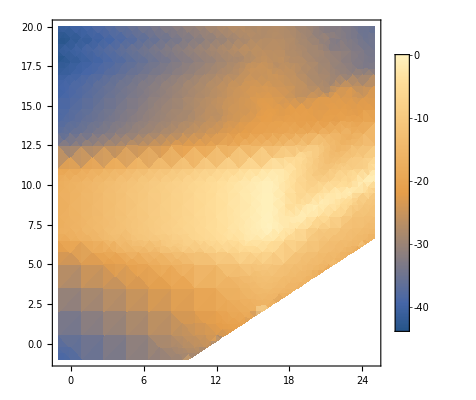

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,-1,20},PlotLegends->Automatic,PlotRange->All](*0th moment no truncation*)
```

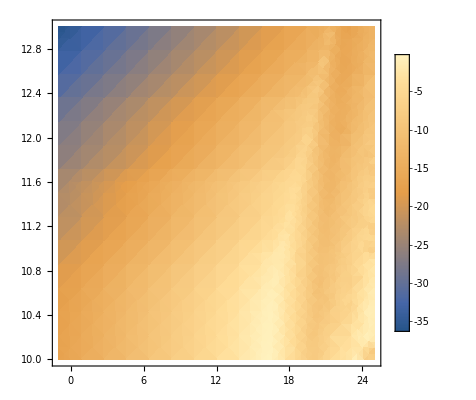

```mathematica
DensityPlot[Log10@Abs@StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,10,13},PlotLegends->Automatic,PlotRange->All](*0th moment no truncation*)
```

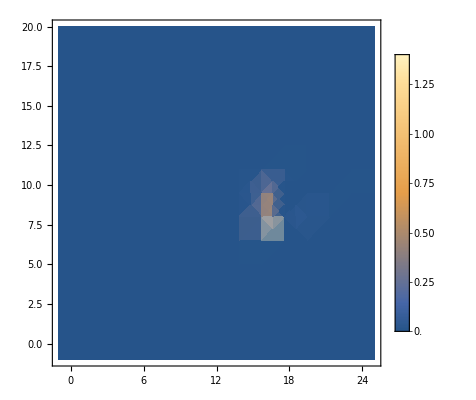

```mathematica
DensityPlot[StructureFunction[10^w,10^k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,-1,25},{k,-1,20},PlotLegends->Automatic,PlotRange->All](*0th moment no truncation*)
```

```mathematica
DensityPlot[StructureFunction[w,k,"m"/.SIConstRepl,10^15,FeTotalparams,4,False],{w,10^14,10^17},{k,10^5,10^10},PlotLegends->Automatic,PlotRange->All](*0th moment no truncation*)
```

-Graphics-

```mathematica
Limit[ϵM[ω/z,z,uν],z->∞]
```

$Aborted

```mathematica
Series[uzLinDielectric[ω,z],{z,∞,1}]
```

Series[1+(χ^2 (1/2+((1-(z-ω)^2) Log[Abs[(1+z-ω)/(1-z+ω)]]+(1-(z+ω)^2) Log[Abs[(1+z+ω)/(1-z-ω)]])/(8 z)+ⅈ (Piecewise[{{(π ω)/2, z+ω<1}, {(π (1-(z-ω)^2))/(8 z), Abs[z-ω]<1<z+ω}, {0, True}}])))/z^2,{z,∞,1}]

```mathematica
Limit[z D[uzLinDielectric[ω,z],z],z->∞]
```

$Aborted

```mathematica
Limit[uzLinDielectric[u,z],z->∞]
```

1

```mathematica
Refine[Series[uzLinDielectric[u/z,z],{z,∞,1}],Assumptions->1<u/z+z]
```

Piecewise[{{Log[Abs[(1-u/z+z)/(1+u/z-z)]] O[1/z]^3+Log[Abs[(1-u/z+z)/(1+u/z-z)]] O[1/z]^5+(1+O[1/z]^2)+Log[Abs[(1-u/z+z)/(1+u/z-z)]] (-χ^2/(8 z)+O[1/z]^2), Abs[-u/z+z]≥1}, {Log[Abs[(1-u/z+z)/(1+u/z-z)]] O[1/z]^3+Log[Abs[(1-u/z+z)/(1+u/z-z)]] O[1/z]^5+Log[Abs[(1-u/z+z)/(1+u/z-z)]] (-χ^2/(8 z)+O[1/z]^2)+(1-(ⅈ χ^2 π)/(8 z)+O[1/z]^2), True}}]

```mathematica
Refine[Series[uzLinDielectric[u,z],{z,∞,6}],Assumptions->{1<u+z,(1-u+z)/(1+u-z)<0}]
```

1+χ^2/(3 z^4)+(χ^2 (1+5 u^2))/(15 z^6)+O[1/z]^7

```mathematica
Refine[Series[ϵRPAC[u,z,uν],{z,∞,6}],Assumptions->1<u+z]
```

{1+χ^2/(3 z^4)+(χ^2 (1+5 u^2-5 uν^2))/(15 z^6)+O[1/z]^7,(2 χ^2 u uν)/(3 z^6)+O[1/z]^7}

```mathematica
Refine[Series[ϵM[u,z,uν],{z,∞,6}],Assumptions->{1<u+z,(1-u+z)/(1+u-z)<0,z>1}]
Refine[Im[-1/%//Normal]//Simplify,Assumptions->Element[z,Reals]]//Simplify
```

1+χ^2/(3 z^4)+(2/3 ⅈ χ^2 u uν+1/15 χ^2 (1+5 u^2-5 uν^2)+1/3 χ^2 (-(ⅈ u^2 uν)/(u+ⅈ uν)+(2 u uν^2)/(u+ⅈ uν)+(ⅈ uν^3)/(u+ⅈ uν)))/z^6+O[1/z]^7

1/15 Im[(χ^2 (1+5 u^2+5 ⅈ u uν+5 z^2))/z^6]

```mathematica
Im[-1/(1+("χ")^2/(3 z^4)+(2/3 ⅈ ("χ")^2 u uν+1/15 ("χ")^2 (1+5 u^2-5 uν^2)+1/3 ("χ")^2 (-(ⅈ u^2 uν)/(u+ⅈ uν)+(2 u uν^2)/(u+ⅈ uν)+(ⅈ uν^3)/(u+ⅈ uν)))/z^6)]//Simplify
Refine[Series[%,{z,∞,6}],Assumptions->Element[{"χ",u,uν},Reals]]
```

-15 Im[z^6/(15 z^6+χ^2 (1+5 u^2+5 ⅈ u uν+5 z^2))]

(χ^2 u uν)/(3 z^6)+O[1/z]^7

```mathematica
1/15 (("χ")^2 (5  u uν))/z^6
%/.uν->("νi"/(2 "vF" "qF" z))/.u->("ℏ"ω)/(2"EF"z)/.z-> k/(2 "qF")
%/.FeTotalparams[[1]]/.{ω->10^22.5,k->10^2.5}
```

(χ^2 u uν)/(3 z^6)

(64 qF^7 νi χ^2 ℏ ω)/(3 EF vF k^8)

3.25898×10^68

```mathematica
Series[1 -χ^2/(8 z) Log[Abs[(1+z)/(1-z)]],{z,∞,2}]
```

1+Log[Abs[1/(1-z)+z/(1-z)]] (-χ^2/(8 z)+O[1/z]^3)

```mathematica
Series[(1+z)/(1-z),{z,∞,2}]
```

-1-2/z-2/z^2+O[1/z]^3

```mathematica
Series[1 -χ^2/(8 z) Log[1+2/z+2/z^2],{z,∞,2}]
```

1-χ^2/(4 z^2)+O[1/z]^3

```mathematica
Asymptotic[Im[-1/uzLinDielectric[u,z]],z->∞]
```

-Im[1/(1+(χ^2 (1/2+((1-(-u+z)^2) Log[Abs[(1-u+z)/(1+u-z)]]+(1-(u+z)^2) Log[Abs[(1+u+z)/(1-u-z)]])/(8 z)+ⅈ (Piecewise[{{(π u)/2, u+z<1}, {(π (1-(-u+z)^2))/(8 z), Abs[-u+z]<1<u+z}, {0, True}}])))/z^2)]

```mathematica
Limit[Im[-1/uzLinDielectric[u/z,z]],z->∞]
```

0

```mathematica
Series[Im[-1/uzLinDielectric[u/z,z]],{z,0,2}]
```

Series[-Im[1/(1+(χ^2 (1/2+((1-(-u/z+z)^2) Log[Abs[(1-u/z+z)/(1+u/z-z)]]+(1-(u/z+z)^2) Log[Abs[(1+u/z+z)/(1-u/z-z)]])/(8 z)+ⅈ (Piecewise[{{(π u)/(2 z), u/z+z<1}, {(π (1-(-u/z+z)^2))/(8 z), Abs[-u/z+z]<1<u/z+z}, {0, True}}])))/z^2)],{z,0,2}]

```mathematica
Series[ϵM[u,z,uν],{u,∞,2}]
```

$Aborted

```mathematica
Limit[ϵM[u,z,uν],u->∞]
```

$Aborted

```mathematica
Refine[Series[uzLinDielectric[u,z],{u,∞,6}],Assumptions->{1<u+z,(1-u+z)/(1+u-z)<0,z>1}]
```

1-χ^2/(3 z^2 u^2)+(χ^2 (-3-5 z^2))/(15 z^2 u^4)+(χ^2 (-3-14 z^2-7 z^4))/(21 z^2 u^6)+O[1/u]^7

```mathematica
uzLinDielectric[u,z]
Refine[%,Assumptions->{Abs[z-u]<1<u+z}]
```

1+(χ^2 (1/2+((1-(-u+z)^2) Log[Abs[(1-u+z)/(1+u-z)]]+(1-(u+z)^2) Log[Abs[(1+u+z)/(1-u-z)]])/(8 z)+ⅈ (Piecewise[{{(π u)/2, u+z<1}, {(π (1-(-u+z)^2))/(8 z), Abs[-u+z]<1<u+z}, {0, True}}])))/z^2

1+(χ^2 (1/2+(ⅈ π (1-(-u+z)^2))/(8 z)+((1-(-u+z)^2) Log[(1-u+z)/(1+u-z)]+(1-(u+z)^2) Log[-(1+u+z)/(1-u-z)])/(8 z)))/z^2

```mathematica
Refine[Series[uzLinDielectric[u,z],{u,∞,2}],Assumptions->{Abs[z-u]<1<u+z}]
```

-(ⅈ χ^2 π u^2)/(4 z^3)+(ⅈ χ^2 π u)/(2 z^2)+(1-(ⅈ χ^2 (-π+π z^2))/(4 z^3))-χ^2/(3 z^2 u^2)+O[1/u]^3

```mathematica
Refine[Series[ϵRPAC[u,z,uν],{u,∞,4}],Assumptions->{Abs[z-u]<1<u+z}]
```

{1-χ^2/(3 z^2 u^2)-(χ^2 (3-15 uν^2+5 z^2))/(15 z^2 u^4)+O[1/u]^5,(2 χ^2 uν)/(3 z^2 u^3)+O[1/u]^5}

```mathematica
Refine[Series[ϵM[u,z,uν],{u,∞,2}],Assumptions->{Abs[z-u]<1<u+z}]
```

Piecewise[{{1-χ^2/(3 u^2)+O[1/u]^3, z==1}, {1-χ^2/(3 z^2 u^2)+O[1/u]^3, True}}]

```mathematica
Refine[Series[ϵM[u,z,uν],{u,∞,4}],Assumptions->{Abs[z-u]<1<u+z}]
```

Piecewise[{{1-χ^2/(3 u^2)+(ⅈ χ^2 uν)/(3 u^3)+(-8 χ^2+5 χ^2 uν^2)/(15 u^4)+O[1/u]^5, z==1}, {1-χ^2/(3 z^2 u^2)+(ⅈ χ^2 uν)/(3 z^2 u^3)+(-3 χ^2+5 χ^2 uν^2-5 χ^2 z^2)/(15 z^2 u^4)+O[1/u]^5, True}}]

```mathematica
Refine[Series[Im[-1/ϵM[u,z,uν]],{u,∞,4}],Assumptions->{Abs[z-u]<1<u+z}]
```

Piecewise[{{-(2 (Im[χ] Re[χ]))/(3 u^2)+(-2 Im[χ] Im[uν] Re[χ]-Im[χ]^2 Re[uν]+Re[χ]^2 Re[uν])/(3 u^3)+(2 (-24 Im[χ] Re[χ]+10 Im[χ]^3 Re[χ]-15 Im[χ] Im[uν]^2 Re[χ]-10 Im[χ] Re[χ]^3-15 Im[χ]^2 Im[uν] Re[uν]+15 Im[uν] Re[χ]^2 Re[uν]+15 Im[χ] Re[χ] Re[uν]^2))/(45 u^4)+O[1/u]^5, z==1}, {-(2 (Im[χ] Re[χ]))/(3 z^2 u^2)+(-2 z^2 Im[χ] Im[uν] Re[χ]-z^2 Im[χ]^2 Re[uν]+z^2 Re[χ]^2 Re[uν])/(3 z^4 u^3)-1/(45 z^8 u^4)2 (9 z^6 Im[χ] Re[χ]+15 z^8 Im[χ] Re[χ]-10 z^4 Im[χ]^3 Re[χ]+15 z^6 Im[χ] Im[uν]^2 Re[χ]+10 z^4 Im[χ] Re[χ]^3+15 z^6 Im[χ]^2 Im[uν] Re[uν]-15 z^6 Im[uν] Re[χ]^2 Re[uν]-15 z^6 Im[χ] Re[χ] Re[uν]^2)+O[1/u]^5, True}}]

```mathematica
(("χ")^2 uν)/(3 z^2 u^3)
%/.uν->("νi"/(2 "vF" "qF" z))/.u->("ℏ"ω)/(2"EF"z)/.z-> k/(2 "qF")
%/.FeTotalparams[[1]]/.{ω->10^22.5,k->10^2.5}
```

(χ^2 uν)/(3 u^3 z^2)

(4 EF^3 νi χ^2)/(3 qF vF ℏ^3 ω^3)

2.2897×10^-20

```mathematica
{("ℏ"ω)/(2"EF"z)/.z-> k/(2 "qF"),k/(2 "qF")}
%/.FeTotalparams[[1]]/.{ω->10^22.5,k->10^2.5}
Abs[z-u]<1<u+z/.u->%[[1]]/.z->%[[2]]
```

{(qF ℏ ω)/(EF k),k/(2 qF)}

{1.18784×10^14,1.0875×10^-8}

False

```mathematica
Refine[Series[Im[-1/ϵRPAC[u,z,uν]],{u,∞,4}],Assumptions->{!(Abs[z-u]<1<u+z),u+z>1}]
```

{-(2 (Im[χ] Re[χ]))/(3 z^2 u^2)+1/u^4(-2/3 Im[χ] Re[χ]-(2 Im[χ] Re[χ])/(5 z^2)+(4 Im[χ]^3 Re[χ])/(9 z^4)-(2 Im[χ] Im[uν]^2 Re[χ])/z^2-(4 Im[χ] Re[χ]^3)/(9 z^4)-(2 Im[χ]^2 Im[uν] Re[uν])/z^2+(2 Im[uν] Re[χ]^2 Re[uν])/z^2+(2 Im[χ] Re[χ] Re[uν]^2)/z^2)+O[1/u]^5,(3 (-z^2 Im[χ]^2 Im[uν]+z^2 Im[uν] Re[χ]^2+2 z^2 Im[χ] Re[χ] Re[uν]) u^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 (-3 z^2 Im[χ]^2 Im[uν]-5 z^4 Im[χ]^2 Im[uν]-5 z^2 Im[χ]^2 Im[uν]^3+3 z^2 Im[uν] Re[χ]^2+5 z^4 Im[uν] Re[χ]^2+5 z^2 Im[uν]^3 Re[χ]^2+6 z^2 Im[χ] Re[χ] Re[uν]+10 z^4 Im[χ] Re[χ] Re[uν]-10 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]-5 z^2 Im[χ]^2 Im[uν] Re[uν]^2+5 z^2 Im[uν] Re[χ]^2 Re[uν]^2-10 z^2 Im[χ] Re[χ] Re[uν]^3) u)/(5 ((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)))-1/u 4 ((81 z^2 Im[χ]^2 Im[uν])/(1400 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^4 Im[χ]^2 Im[uν])/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^6 Im[χ]^2 Im[uν])/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ]^2 Im[uν]^3)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ]^2 Im[uν]^3)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^2 Im[χ]^2 Im[uν]^5)/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(81 z^2 Im[uν] Re[χ]^2)/(1400 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^4 Im[uν] Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^6 Im[uν] Re[χ]^2)/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[uν]^3 Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^4 Im[uν]^3 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^2 Im[uν]^5 Re[χ]^2)/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(81 z^2 Im[χ] Re[χ] Re[uν])/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^4 Im[χ] Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^6 Im[χ] Re[χ] Re[uν])/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν])/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ]^2 Im[uν] Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ]^2 Im[uν] Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^2 Im[χ]^2 Im[uν]^3 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[uν] Re[χ]^2 Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^4 Im[uν] Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^2 Im[uν]^3 Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ] Re[χ] Re[uν]^3)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ] Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ]^2 Im[uν] Re[uν]^4)/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[uν] Re[χ]^2 Re[uν]^4)/(8 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^2 Im[χ] Re[χ] Re[uν]^5)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)))-1/u^3 4 ((11 z^2 Im[χ]^2 Im[uν]^3)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^4 Im[χ]^2 Im[uν]^3)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^6 Im[χ]^2 Im[uν]^3)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^8 Im[χ]^2 Im[uν]^3)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ]^2 Im[uν]^5)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ]^2 Im[uν]^5)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ]^2 Im[uν]^5)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^2 Im[χ]^2 Im[uν]^7)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^4 Im[χ]^2 Im[uν]^7)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^2 Im[χ]^2 Im[uν]^9)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(11 z^2 Im[uν]^3 Re[χ]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^4 Im[uν]^3 Re[χ]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^6 Im[uν]^3 Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^8 Im[uν]^3 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^2 Im[uν]^5 Re[χ]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^4 Im[uν]^5 Re[χ]^2)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^6 Im[uν]^5 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^2 Im[uν]^7 Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^4 Im[uν]^7 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^2 Im[uν]^9 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(11 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^6 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^8 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν])/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ] Im[uν]^4 Re[χ] Re[uν])/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ] Im[uν]^4 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(27 z^2 Im[χ] Im[uν]^6 Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^4 Im[χ] Im[uν]^6 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^2 Im[χ] Im[uν]^8 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(11 z^2 Im[χ]^2 Im[uν] Re[uν]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^4 Im[χ]^2 Im[uν] Re[uν]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^6 Im[χ]^2 Im[uν] Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^8 Im[χ]^2 Im[uν] Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ]^2 Im[uν]^3 Re[uν]^2)/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ]^2 Im[uν]^3 Re[uν]^2)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ]^2 Im[uν]^3 Re[uν]^2)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^2 Im[χ]^2 Im[uν]^5 Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^4 Im[χ]^2 Im[uν]^5 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(6 z^2 Im[χ]^2 Im[uν]^7 Re[uν]^2)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(11 z^2 Im[uν] Re[χ]^2 Re[uν]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^4 Im[uν] Re[χ]^2 Re[uν]^2)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^6 Im[uν] Re[χ]^2 Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^8 Im[uν] Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^2 Im[uν]^3 Re[χ]^2 Re[uν]^2)/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^4 Im[uν]^3 Re[χ]^2 Re[uν]^2)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^6 Im[uν]^3 Re[χ]^2 Re[uν]^2)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^2 Im[uν]^5 Re[χ]^2 Re[uν]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^4 Im[uν]^5 Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(6 z^2 Im[uν]^7 Re[χ]^2 Re[uν]^2)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(11 z^2 Im[χ] Re[χ] Re[uν]^3)/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^4 Im[χ] Re[χ] Re[uν]^3)/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^6 Im[χ] Re[χ] Re[uν]^3)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^8 Im[χ] Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/(35 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(30 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ] Im[uν]^4 Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ]^2 Im[uν] Re[uν]^4)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ]^2 Im[uν] Re[uν]^4)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ]^2 Im[uν] Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^2 Im[χ]^2 Im[uν]^3 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^4 Im[χ]^2 Im[uν]^3 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(21 z^2 Im[χ]^2 Im[uν]^5 Re[uν]^4)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(117 z^2 Im[uν] Re[χ]^2 Re[uν]^4)/(140 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^4 Im[uν] Re[χ]^2 Re[uν]^4)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^6 Im[uν] Re[χ]^2 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^2 Im[uν]^3 Re[χ]^2 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[uν]^3 Re[χ]^2 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(21 z^2 Im[uν]^5 Re[χ]^2 Re[uν]^4)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(117 z^2 Im[χ] Re[χ] Re[uν]^5)/(70 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^4 Im[χ] Re[χ] Re[uν]^5)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^6 Im[χ] Re[χ] Re[uν]^5)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^5)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(3 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν]^5)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(21 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν]^5)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(27 z^2 Im[χ]^2 Im[uν] Re[uν]^6)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^4 Im[χ]^2 Im[uν] Re[uν]^6)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(27 z^2 Im[uν] Re[χ]^2 Re[uν]^6)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(9 z^4 Im[uν] Re[χ]^2 Re[uν]^6)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(9 z^2 Im[χ] Re[χ] Re[uν]^7)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^4 Im[χ] Re[χ] Re[uν]^7)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(12 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^7)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(15 z^2 Im[χ]^2 Im[uν] Re[uν]^8)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(15 z^2 Im[uν] Re[χ]^2 Re[uν]^8)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)+(3 z^2 Im[χ] Re[χ] Re[uν]^9)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)^2)-(243 z^2 Im[χ]^2 Im[uν])/(3500 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(297 z^4 Im[χ]^2 Im[uν])/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^6 Im[χ]^2 Im[uν])/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^8 Im[χ]^2 Im[uν])/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(297 z^2 Im[χ]^2 Im[uν]^3)/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^4 Im[χ]^2 Im[uν]^3)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^6 Im[χ]^2 Im[uν]^3)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[χ]^2 Im[uν]^5)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^4 Im[χ]^2 Im[uν]^5)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^2 Im[χ]^2 Im[uν]^7)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(243 z^2 Im[uν] Re[χ]^2)/(3500 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(297 z^4 Im[uν] Re[χ]^2)/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^6 Im[uν] Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^8 Im[uν] Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(297 z^2 Im[uν]^3 Re[χ]^2)/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(27 z^4 Im[uν]^3 Re[χ]^2)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^6 Im[uν]^3 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[uν]^5 Re[χ]^2)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[uν]^5 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^2 Im[uν]^7 Re[χ]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(243 z^2 Im[χ] Re[χ] Re[uν])/(1750 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(297 z^4 Im[χ] Re[χ] Re[uν])/(350 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^6 Im[χ] Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^8 Im[χ] Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(297 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(350 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(5 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^6 Im[χ] Im[uν]^2 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν])/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^4 Im[χ] Im[uν]^4 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(15 z^2 Im[χ] Im[uν]^6 Re[χ] Re[uν])/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(297 z^2 Im[χ]^2 Im[uν] Re[uν]^2)/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^4 Im[χ]^2 Im[uν] Re[uν]^2)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^6 Im[χ]^2 Im[uν] Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ]^2 Im[uν]^3 Re[uν]^2)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ]^2 Im[uν]^3 Re[uν]^2)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^2 Im[χ]^2 Im[uν]^5 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(297 z^2 Im[uν] Re[χ]^2 Re[uν]^2)/(700 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(27 z^4 Im[uν] Re[χ]^2 Re[uν]^2)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^6 Im[uν] Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[uν]^3 Re[χ]^2 Re[uν]^2)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^4 Im[uν]^3 Re[χ]^2 Re[uν]^2)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(27 z^2 Im[uν]^5 Re[χ]^2 Re[uν]^2)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(297 z^2 Im[χ] Re[χ] Re[uν]^3)/(350 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^4 Im[χ] Re[χ] Re[uν]^3)/(5 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^6 Im[χ] Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/(5 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(3 z^4 Im[χ] Im[uν]^2 Re[χ] Re[uν]^3)/((Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(15 z^2 Im[χ] Im[uν]^4 Re[χ] Re[uν]^3)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(27 z^2 Im[χ]^2 Im[uν] Re[uν]^4)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^4 Im[χ]^2 Im[uν] Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(15 z^2 Im[χ]^2 Im[uν]^3 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^2 Im[uν] Re[χ]^2 Re[uν]^4)/(20 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(9 z^4 Im[uν] Re[χ]^2 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(15 z^2 Im[uν]^3 Re[χ]^2 Re[uν]^4)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(9 z^2 Im[χ] Re[χ] Re[uν]^5)/(10 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^4 Im[χ] Re[χ] Re[uν]^5)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(27 z^2 Im[χ] Im[uν]^2 Re[χ] Re[uν]^5)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(15 z^2 Im[χ]^2 Im[uν] Re[uν]^6)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))+(15 z^2 Im[uν] Re[χ]^2 Re[uν]^6)/(4 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2))-(3 z^2 Im[χ] Re[χ] Re[uν]^7)/(2 (Im[χ]^2+Re[χ]^2)^2 (Im[uν]^2+Re[uν]^2)))+O[1/u]^5}

```mathematica
Refine[Series[ϵM[u,z,uν],{u,∞,4}],Assumptions->{!(Abs[z-u]<1<u+z),u+z>1}]
```

Piecewise[{{1-χ^2/(3 u^2)+(ⅈ χ^2 uν)/(3 u^3)+(-8 χ^2+5 χ^2 uν^2)/(15 u^4)+O[1/u]^5, z==1}, {1-χ^2/(3 z^2 u^2)+(ⅈ χ^2 uν)/(3 z^2 u^3)+(-3 χ^2+5 χ^2 uν^2-5 χ^2 z^2)/(15 z^2 u^4)+O[1/u]^5, True}}]

#### Interpolate the structure function

What is the range of u and z that we need to interpolate over?

```mathematica
Solve[k v - ℏ k^2/(2 m)-ω==0,k]
%/.ω->1/(2 ℏ)m v^2//Simplify
{1/(2 ℏ)m v^2,%}/.ℏ->"ℏ"/.{m->"m"/.SIConstRepl,v->10^5}/.Constants`SIConstRepl
```

{{k→-(m (-v+(√(m v^2-2 ω ℏ))/(√m)))/ℏ},{k→(m v+√m √(m v^2-2 ω ℏ))/ℏ}}

{{k→(m v)/ℏ},{k→(m v)/ℏ}}

{4.31754×10^13,{{k→8.63507×10^8},{k→8.63507×10^8}}}

```mathematica
Print["So max is:"]
kmax =(m v)/ℏ
ωmax = 1/(2 ℏ)m v^2
Print["duh, this gives for u and z"]
umax = ωmax/(vF kmax)
zmax = kmax/(2 kF)
Print["This implies"]
```

So max is:

(m v)/ℏ

(m v^2)/(2 ℏ)

duh, this gives for u and z

v/(2 vF)

(m v)/(2 kF ℏ)

This implies

Max vχ is 0.2 c, max mχ is 1 PeV

```mathematica
mmax = 10^15("JpereV")/("c")^2/.Constants`SIConstRepl
vmax = 0.2 "c"/.Constants`SIConstRepl
```

1.78×10^-21

6.×10^7

```mathematica
(m v)/("ℏ")/.{m->mmax,v->vmax}/.SIConstRepl
 1/(2 "ℏ")m v^2/.{m->mmax,v->vmax}/.SIConstRepl
umax /.{v->vmax,m->mmax}/.vF->"vF"/.FeTotalparams
zmax /.{v->vmax,m->mmax}/.ℏ->"ℏ"/.kF->"qF"/.vF->"vF"/.FeTotalparams
Max[%]
```

9.47867×10^33 mmax vmax

4.73934×10^33 mmax vmax^2

{2.96959×10^-7 vmax,2.42111×10^-7 vmax,1.8428×10^-7 vmax,9.49171×10^-8 vmax,1.87103×10^-8 vmax,4.08064×10^-9 vmax}

{3.2597×10^23 mmax vmax,2.65764×10^23 mmax vmax,2.02284×10^23 mmax vmax,1.0419×10^23 mmax vmax,2.05382×10^22 mmax vmax,4.47929×10^21 mmax vmax}

Max[4.47929×10^21 mmax vmax,2.05382×10^22 mmax vmax,1.0419×10^23 mmax vmax,2.02284×10^23 mmax vmax,2.65764×10^23 mmax vmax,3.2597×10^23 mmax vmax]

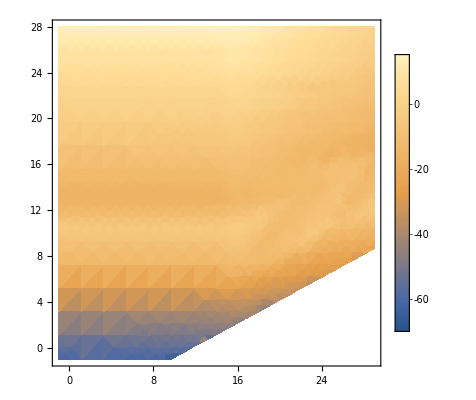

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,False],{w,-1,29},{k,-1,28},PlotLegends->Automatic](*4th moment*)
```

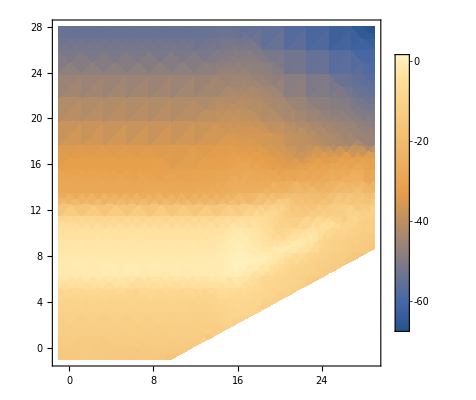

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,0,False],{w,-1,29},{k,-1,28},PlotLegends->Automatic](*0th moment*)
```

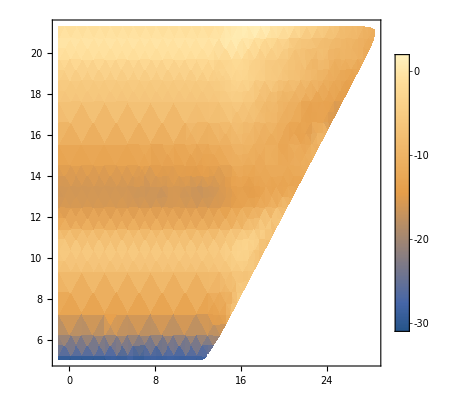

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,True],{w,-1,29},{k,-1,28},PlotLegends->Automatic,PlotRange->All](*4th moment*)
```

```mathematica
Clear[StructureFunction]
```

```mathematica
StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,True]/.{w->2,k->2}
StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,False]/.{w->2,k->2}
```

0.

7.20413×10^-47

```mathematica
StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,False]
```

```mathematica
Solve[k v - ℏ k^2/(2 m)-ω==0,k]
(k/.%[[2]])-(k/.%[[1]])//Simplify
kofξ = (k/.%%[[1]])+ ξ ((k/.%%[[2]])-(k/.%%[[1]]))//Simplify
```

{{k→-(m (-v+(√(m v^2-2 ω ℏ))/(√m)))/ℏ},{k→(m v+√m √(m v^2-2 ω ℏ))/ℏ}}

(2 √m √(m v^2-2 ω ℏ))/ℏ

(m v+√m (-1+2 ξ) √(m v^2-2 ω ℏ))/ℏ

```mathematica
StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,False]/.{w->2,k->2}
```

```mathematica
(*Clear[Interpolateϵtest]
Interpolateϵtest[]:=Module[{mmax,vmax,ωmax,kmax,ωmaxminrat,kmaxminrat,gridsize=200,Interpointsω,Interpointsk,Interpointsωandk,Interpointsϵ,Interϵf},
mmax = 10^15("JpereV")/("c")^2/.Constants`SIConstRepl;
vmax = 0.2 "c"/.Constants`SIConstRepl;
kmax = (mmax vmax)/("ℏ")/.SIConstRepl;
ωmax= (mmax vmax^2)/(2 "ℏ")/.SIConstRepl;
ωmaxminrat = 10^-30;
kmaxminrat = 10^-20;

Interpointsω=10^Subdivide[Log10[ωmaxminrat ωmax],Log10[ωmax],gridsize];
Interpointsk=10^Subdivide[Log10[kmaxminrat kmax],Log10[kmax],gridsize];

Interpointsωandk =Table[ Table[{Interpointsk[[i]],Interpointsω[[j]]},{i,gridsize}],{j,gridsize}];

Interpointsϵ=Table[ Table[{{Interpointsk[[i]],Interpointsω[[j]]},10^-60+StructureFunction[Interpointsk[[i]],Interpointsω[[j]],mmax,vmax,FeTotalparams,0,False]},{i,gridsize}],{j,gridsize}];

Interϵf=Interpolation[Flatten[Log10[Interpointsϵ],1],InterpolationOrder->3];

Interϵf
]*)
```

```mathematica
Interϵftest = AbsoluteTiming@Interpolateϵtest[]
```

{75.2104,InterpolatingFunction[…]}

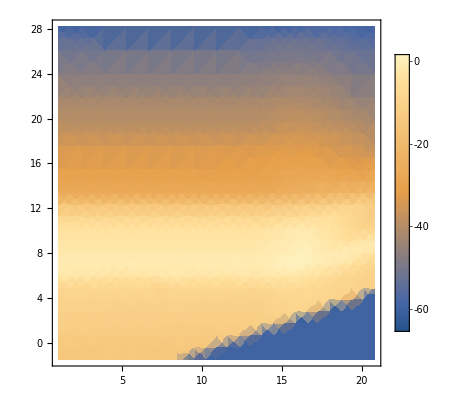

```mathematica
DensityPlot[Interϵftest[[2]][k,ω],{k,1.02,20.8},{ω,-1.5,28.2},PlotLegends->Automatic]
```

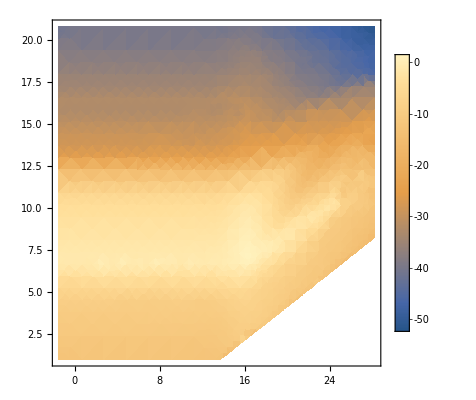

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,0,False],{w,-1.5,28.2},{k,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

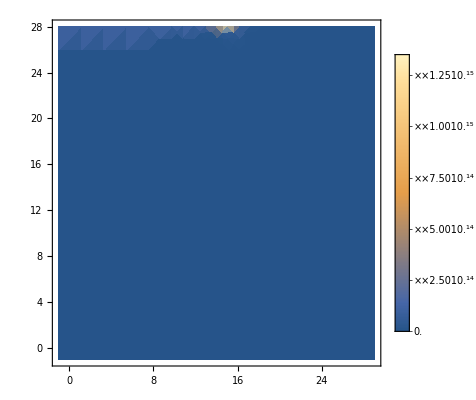

```mathematica
DensityPlot[N[StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,4,False],50],{w,-1,29},{k,-1,28},PlotLegends->Automatic,PlotRange->All](*4th moment*)
```

```mathematica
DensityPlot[N[StructureFunction[w,k,mmax,vmax,FeTotalparams,4,False],50],{w,10^-1,10^29},{k,10^-1,10^28},PlotLegends->Automatic,PlotRange->All](*4th moment*)
```

-Graphics-

#### Interpolate structure function u and z

```mathematica
StructureFunction[ω_,k_?NumberQ,mχ_,vχ_,params_,n_:0,truncate_:True,cut_:4]:=Abs@Sum[(2 ("e")^2/(vχ "ℏ" (2 π)^2 "ϵ0") (1+If[cut > "β" "ℏ" ω,(1/(1-E^(- "β" "ℏ" ω))-1),0])/.params[[i]])(z^n/z /.z->k/(2 "qF")/.params[[i]])If[truncate,kinTheta[ω,k,mχ,vχ],1]Im[-("Ai"/.params[[i]]) / Dielectrics`ϵMNum[("ℏ"ω)/(2"EF"z)/.z->k/(2 "qF")/.params[[i]], k/(2 "qF")/.params[[i]], uνFit[z]/.z-> k/(2 "qF")/. params[[i]], params[[i]]]],{i,Length[params]}]
```

```mathematica
Clear[StructureFunctionuz]
StructureFunctionuz[u_,z_?NumberQ,params_,cut_:4]:=(*ω = (4 kF vF u z) *)Abs@Sum[ (2(1+If[cut > "β" "ℏ" (4 "qF" "vF" u z),(1/(1-E^(- "β" "ℏ" (2 "qF" "vF" u z)))-1),0])/.params[[i]])((4"ϵ0" ("qF")^2 z^2)/("e")^2)Im[-("Ai"/.params[[i]]) / Dielectrics`ϵM[u, z,("νi"/(2 "vF" "qF" z))]]/.params[[i]],{i,Length[params]}]
```

```mathematica
Solve[{u ==ω/(k vF),z==k/(2 kF)},{ω,k}]
```

{{ω→2 kF u vF z,k→2 kF z}}

```mathematica
(ϵ0 k^2)/e^2/.k->2 qF z
```

(4 qF^2 z^2 ϵ0)/e^2

```mathematica
AbsoluteTiming@StructureFunctionuz[100,100,FeTotalparams]
```

{0.0158729,1.58559×10^45}

1.78×10^-21

6.×10^7

```mathematica
mmax = 10^15("JpereV")/("c")^2/.Constants`SIConstRepl
vmax = 0.2 "c"/.Constants`SIConstRepl
(m v)/("ℏ")/.{m->mmax,v->vmax}/.SIConstRepl
 1/(2 "ℏ")m v^2/.{m->mmax,v->vmax}/.SIConstRepl
umax /.{v->vmax,m->mmax}/.vF->"vF"/.FeTotalparams
zmax /.{v->vmax,m->mmax}/.ℏ->"ℏ"/.kF->"qF"/.vF->"vF"/.FeTotalparams
```

1.78×10^-21

6.×10^7

1.01232×10^21

3.03697×10^28

{17.8175,14.5267,11.0568,5.69503,1.12262,0.244838}

{3.48136×10^10,2.83836×10^10,2.16039×10^10,1.11275×10^10,2.19348×10^9,4.78389×10^8}

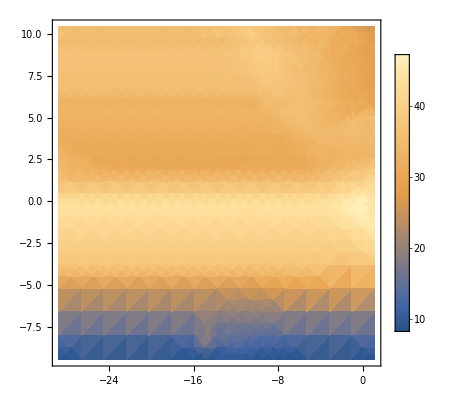

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,interstructest[[2]]["Domain"][[1,1]],interstructest[[2]]["Domain"][[1,2]]},{z,interstructest[[2]]["Domain"][[2,1]],interstructest[[2]]["Domain"][[2,2]]},PlotLegends->Automatic]
```

```mathematica
Clear[StructureFunctionuz]
```

```mathematica
StructureFunctionuz[10^-29,10^-10,FeTotalparams]
```

1.5344×10^6

```mathematica
Series[1/(1-E^(-  uz))-1,{uz,0,1}]//Normal
{%,1/uz-1/2}/.uz->0.01
```

-1/2+1/uz+uz/12

{99.5008,99.5}

{0.0035838,1.5344×10^6}

#### Test interpolation with dσdER

InterpolatingFunction[…]

```mathematica
Clear[dσdERe]
```

```mathematica
(*dσdERetest[ω_,mχ_,vχ_,params_,β_,cut_:4]:= NIntegrate[10^Interϵftest[[2]][Log10@k,Log10@ω],{k,Dielectrics`kb["-",ω,mχ,vχ],Dielectrics`kb["+",ω,mχ,vχ]}]
*)
```

```mathematica
AbsoluteTiming@dσdERetest[10^20/3,1/2 mmax,1/2 vmax,FeTotalparams[[1]],"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.38289×10^18}. NIntegrate obtained 8.27974×10^-21 and 2.19557×10^-24 for the integral and error estimates.

{0.0341324,8.27974×10^-21}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {100.17989044257577546659376821480691432952880859375}. NIntegrate obtained 6.41498×10^-17 and 1.17045×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {110.40345355768639734606040292419493198394775390625}. NIntegrate obtained 1.80475×10^-15 and 1.32135×10^-20 for the integral and error estimates.

{0.586537,1.36989×10^-19}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {436.986}. NIntegrate obtained 2.02667×10^-16 and 6.60127×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {356.275}. NIntegrate obtained 6.41519×10^-17 and 2.08929×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {271.175}. NIntegrate obtained 1.80516×10^-15 and 5.87739×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.36252,1.3711×10^-19}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

{0.356336,1.39977×10^-20}

```mathematica
AbsoluteTiming@dσdERe[10^15,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

{0.221557,0.0000118372}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {436.986}. NIntegrate obtained 2.02644×10^-16 and 6.58351×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {356.275}. NIntegrate obtained 6.41413×10^-17 and 2.09968×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {271.175}. NIntegrate obtained 1.80463×10^-15 and 5.88023×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.55159,1.36985×10^-19}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {469.495}. NIntegrate obtained 1.70779×10^-21 and 4.35648×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {373.422}. NIntegrate obtained 3.26739×10^-24 and 7.77352×10^-30 for the integral and error estimates.

{0.614665,1.36989×10^-19}

```mathematica
AbsoluteTiming@dσdERe[10^20,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {436.986}. NIntegrate obtained 2.02667×10^-16 and 6.60127×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {362.815}. NIntegrate obtained 3.61294×10^-17 and 6.05907×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {300.039}. NIntegrate obtained 1.06999×10^-16 and 3.57443×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.546434,1.36989×10^-19}

```mathematica
AbsoluteTiming@dσdERe[10^8,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.51812}. NIntegrate obtained 2.28421×10^-8 and 5.80719×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.23772}. NIntegrate obtained 2.14666×10^-9 and 1.39069×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.94208}. NIntegrate obtained 1.01426×10^-8 and 2.56441×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.542566,7.12935×10^-7}

```mathematica
AbsoluteTiming@dσdERe[10^8,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.51812}. NIntegrate obtained 2.28421×10^-8 and 5.80719×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.23772}. NIntegrate obtained 2.14666×10^-9 and 1.39069×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.94208}. NIntegrate obtained 1.01426×10^-8 and 2.56441×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.567825,7.12935×10^-7}

```mathematica
AbsoluteTiming@dσdERe[10^□,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.51812}. NIntegrate obtained 2.28384×10^-8 and 5.80374×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.23772}. NIntegrate obtained 1.67337×10^-9 and 3.44232×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.94208}. NIntegrate obtained 9.67146×10^-9 and 7.52343×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.587322,7.01863×10^-7}

```mathematica
AbsoluteTiming@dσdERe[10^8,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.51812}. NIntegrate obtained 2.28384×10^-8 and 5.80374×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.23772}. NIntegrate obtained 1.67337×10^-9 and 3.44232×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.94208}. NIntegrate obtained 9.67146×10^-9 and 7.52343×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.563174,7.01863×10^-7}

```mathematica
Interϵftest[[2]][#1,20]&
NIntegrate[%[Log10@k],{k,10^10,10^20}]
```

Interϵftest⟦2⟧[#1,20]&

-4.1405×10^21

```mathematica
10^Interϵftest[[2]][20,20]
```

1.58043×10^-42

{{{-18.7492,-9.45825},8.35294},{{-18.7158,-9.45825},8.35294},{{-18.6825,-9.45825},8.35294},{{-18.6492,-9.45825},8.35294},{{-18.6158,-9.45825},8.35294}}

{721.948,InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>]}

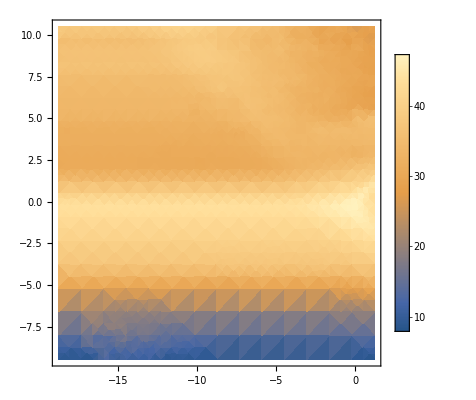

```mathematica
interstructest=AbsoluteTiming@InterpolateStrucuz[FeTotalparams]
DensityPlot[interstructest[[2]][u,z],{u,interstructest[[2]]["Domain"][[1,1]],interstructest[[2]]["Domain"][[1,2]]},{z,interstructest[[2]]["Domain"][[2,1]],interstructest[[2]]["Domain"][[2,2]]},PlotLegends->Automatic]
```

```mathematica
interstruc=AbsoluteTiming@InterpolateStrucuzIndivOsc[FeTotalparams]
```

{656.992,{{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}}}}

```mathematica
DensityPlot[interstructest[[2]][u,z],{u,interstructest[[2]]["Domain"][[1,1]],interstructest[[2]]["Domain"][[1,2]]},{z,interstructest[[2]]["Domain"][[2,1]],interstructest[[2]]["Domain"][[2,2]]},PlotLegends->Automatic]
```

```mathematica
SaveIt[NotebookDirectory[]<>"InterStrucFe",interstruc[[2]]]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\InterStrucFe.dat

```mathematica
ReadIt[NotebookDirectory[]<>"../capture/InterStrucFe"]
```

{{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}}}

```mathematica
dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}

InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>]

{7.11364×10^-7,2160.39}

0.01849 Null

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl]
```

#### z integrand

```mathematica
interstructest=AbsoluteTiming@InterpolatezIntegranduzIndivOsc[FeTotalparams]
```

{660.769,{{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}},{InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>],{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}}}}

```mathematica
SaveIt[NotebookDirectory[]<>"InterStrucFe",interstruc[[2]]]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\InterStrucFe.dat

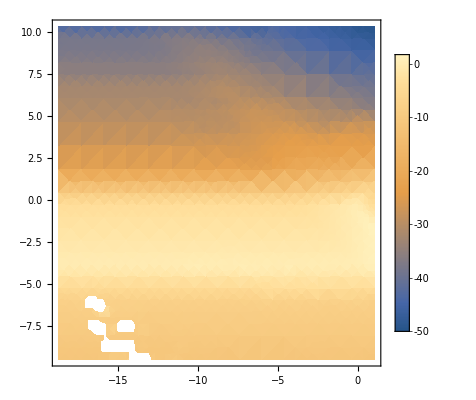

```mathematica
DensityPlot[interstructest[[3]][u,z],{u,interstructest[[3]]["Domain"][[1,1]],interstructest[[3]]["Domain"][[1,2]]},{z,interstructest[[3]]["Domain"][[2,1]],interstructest[[3]]["Domain"][[2,2]]},PlotLegends->Automatic,PlotRange->All]
```

```mathematica
interstructest[[2]][[;;,1]]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}

InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>]

{7.11364×10^-7,2160.39}

$Aborted

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl,interstruc[[2]]]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}

InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>]

{7.11364×10^-7,2160.39}

$Aborted

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl,interstruc[[2]]]
```

2.36364×10^36

10^(InterpolatingFunction[{{-18.7492, 1.21751}, {-9.45825, 10.5084}}, <>][Log[(2.04248×10^-7)/(EnergyLoss`Private`z)]/Log[10],Log[EnergyLoss`Private`z]/Log[10]])

1.50477×10^43

{58.9404,Null}

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl,interstruc[[2]]]
```

1.50477×10^43

{56.8687,Null}

```mathematica
Clear[]
```

```mathematica
AbsoluteTiming@dσdEReInterp[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl,interstruc[[2]]]
```

{340.396,1.56557×10^43}

```mathematica
AbsoluteTiming@dσdERe[10^10,10^10("JpereV")/("c")^2/.SIConstRepl,10^-3"c"/.SIConstRepl,FeTotalparams,"β"/.FeTotalparams]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00160105}. NIntegrate obtained 1.76913×10^-6 and 3.47617×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00130534}. NIntegrate obtained 1.95976×10^-7 and 3.57675×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000993544}. NIntegrate obtained 9.81427×10^-7 and 6.3244×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.616517,1.50102×10^-6}

```mathematica
AbsoluteTiming@dσdERe[10^-6 mmax/2 vmax^2/("ℏ")/.SIConstRepl,1/2 mmax,1/2 vmax,FeTotalparams,"β"/.FeTotalparams]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {102776.}. NIntegrate obtained 3.11099×10^-23 and 9.45615×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {284986.}. NIntegrate obtained 5.75583×10^-24 and 1.26161×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {63778.3}. NIntegrate obtained 6.56096×10^-23 and 2.1718×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.558333,3.61818×10^-27}

```mathematica
Refine[If[4 >#,If[#>0.01,1/(1-E^(- #)),1/#-1/2],1]&[x],Assumptions->{x>4,4>x>0.01,0.01>x}[[3]]]
```

-1/2+1/x

```mathematica
Series[1/(1-E^(- x)),{x,0,1}]
```

1/x+1/2+x/12+O[x]^2

#### Series Expansion of z

```mathematica
Series[Im[-1/ϵM[u,z,uν]],{z,∞,4}]
```

-Im[1/(1+((χ^2 (u+ⅈ uν))/(3 z^4)+O[1/z]^5)/(u+((2 ⅈ uν)/(3 z^2)-(2 ⅈ uν (-1-5 u^2-10 ⅈ u uν+5 uν^2))/(15 z^4)+O[1/z]^5)/(1+Log[(z+1+O[1/z]^5)/Abs[1-z]] (-z/2+1/(2 z)+O[1/z]^5))))]

```mathematica
-Im[1/(1+((("χ")^2 (u+ⅈ uν))/(3 z^4)+O[1/z]^5)/(u+((2 ⅈ uν)/(3 z^2)-(2 ⅈ uν (-1-5 u^2-10 ⅈ u uν+5 uν^2))/(15 z^4)+O[1/z]^5)/(1+Log[(z+1+O[1/z]^5)/Abs[1-z]] (-z/2+1/(2 z)+O[1/z]^5))))]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}]
cexpandedlargez=ComplexExpand[%]//Simplify
```

-Im[1/(1+(χ^2 (u+ⅈ uν))/(3 z^4 (u-(4 ⅈ uν (1+5 u^2+10 ⅈ u uν-5 uν^2+5 z^2))/(15 z^3 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]])))))]

-Im[1/(1+((u+ⅈ uνt) χ^2)/(3 z^4 (u-(4 ⅈ uνt (1+5 u^2+10 ⅈ u uνt-5 uνt^2+5 z^2))/(15 z^3 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]])))))]

-Im[1/(1+((u+ⅈ uνt) χ^2)/(3 z^4 (u-(4 ⅈ uνt (1+5 u^2+10 ⅈ u uνt-5 uνt^2+5 z^2))/(15 z^3 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]])))))]

(5 uνt z χ^2 (16 uνt (-1+5 u^2+5 uνt^2-5 z^2) (-1+z^2) Arg[1+z]+60 u z^3 (-1+z^2)^2 Arg[1+z]^2+u (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]) (-4 (2+10 u^2+10 uνt^2+10 z^2-15 z^4)+15 z^3 (-1+z^2) Log[(-1+z)^2]-15 z^3 (-1+z^2) Log[(1+z)^2])))/(64 uνt^2 z^2+640 u^2 uνt^2 z^2+1600 u^4 uνt^2 z^2-640 uνt^4 z^2+3200 u^2 uνt^4 z^2+1600 uνt^6 z^2+640 uνt^2 z^4+3200 u^2 uνt^2 z^4-3200 uνt^4 z^4+1600 uνt^2 z^6-9600 u^2 uνt^2 z^6+3600 u^2 z^10+320 uνt^2 z^2 χ^2-1600 u^2 uνt^2 z^2 χ^2-1600 uνt^4 z^2 χ^2+1600 uνt^2 z^4 χ^2+2400 u^2 z^6 χ^2+400 u^2 z^2 χ^4+400 uνt^2 z^2 χ^4-160 u uνt z (-1+z^2) (3 (1+5 u^2-5 uνt^2) z^4+15 z^6+(1+5 u^2+5 uνt^2) χ^2+5 z^2 χ^2) Arg[1+z]+100 (-1+z^2)^2 (uνt^2 χ^4+u^2 (3 z^4+χ^2)^2) Arg[1+z]^2+25 (-1+z^2)^2 (uνt^2 χ^4+u^2 (3 z^4+χ^2)^2) Log[(-1+z)^2]^2-2400 u^2 uνt^2 z^5 Log[(1+z)^2]+2400 u^2 uνt^2 z^7 Log[(1+z)^2]+1800 u^2 z^9 Log[(1+z)^2]-1800 u^2 z^11 Log[(1+z)^2]+80 uνt^2 z χ^2 Log[(1+z)^2]-400 u^2 uνt^2 z χ^2 Log[(1+z)^2]-400 uνt^4 z χ^2 Log[(1+z)^2]+320 uνt^2 z^3 χ^2 Log[(1+z)^2]+400 u^2 uνt^2 z^3 χ^2 Log[(1+z)^2]+400 uνt^4 z^3 χ^2 Log[(1+z)^2]+1200 u^2 z^5 χ^2 Log[(1+z)^2]-400 uνt^2 z^5 χ^2 Log[(1+z)^2]-1200 u^2 z^7 χ^2 Log[(1+z)^2]+200 u^2 z χ^4 Log[(1+z)^2]+200 uνt^2 z χ^4 Log[(1+z)^2]-200 u^2 z^3 χ^4 Log[(1+z)^2]-200 uνt^2 z^3 χ^4 Log[(1+z)^2]+225 u^2 z^8 Log[(1+z)^2]^2-450 u^2 z^10 Log[(1+z)^2]^2+225 u^2 z^12 Log[(1+z)^2]^2+150 u^2 z^4 χ^2 Log[(1+z)^2]^2-300 u^2 z^6 χ^2 Log[(1+z)^2]^2+150 u^2 z^8 χ^2 Log[(1+z)^2]^2+25 u^2 χ^4 Log[(1+z)^2]^2+25 uνt^2 χ^4 Log[(1+z)^2]^2-50 u^2 z^2 χ^4 Log[(1+z)^2]^2-50 uνt^2 z^2 χ^4 Log[(1+z)^2]^2+25 u^2 z^4 χ^4 Log[(1+z)^2]^2+25 uνt^2 z^4 χ^4 Log[(1+z)^2]^2-10 (-1+z^2) Log[(-1+z)^2] (-4 uνt^2 z χ^2 (2-10 uνt^2+10 z^2+5 χ^2)+20 u^2 z (-(3 z^4+χ^2)^2+2 uνt^2 (6 z^4+χ^2))+5 (-1+z^2) (uνt^2 χ^4+u^2 (3 z^4+χ^2)^2) Log[(1+z)^2]))

```mathematica
Arg[1+z]/.Arg[1+z]->0
```

0

```mathematica
cexpandedlargez/.Arg[1+z]->0
Series[%,{z,∞,6}]
```

(5 u uνt z χ^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]) (-4 (2+10 u^2+10 uνt^2+10 z^2-15 z^4)+15 z^3 (-1+z^2) Log[(-1+z)^2]-15 z^3 (-1+z^2) Log[(1+z)^2]))/(64 uνt^2 z^2+640 u^2 uνt^2 z^2+1600 u^4 uνt^2 z^2-640 uνt^4 z^2+3200 u^2 uνt^4 z^2+1600 uνt^6 z^2+640 uνt^2 z^4+3200 u^2 uνt^2 z^4-3200 uνt^4 z^4+1600 uνt^2 z^6-9600 u^2 uνt^2 z^6+3600 u^2 z^10+320 uνt^2 z^2 χ^2-1600 u^2 uνt^2 z^2 χ^2-1600 uνt^4 z^2 χ^2+1600 uνt^2 z^4 χ^2+2400 u^2 z^6 χ^2+400 u^2 z^2 χ^4+400 uνt^2 z^2 χ^4+25 (-1+z^2)^2 (uνt^2 χ^4+u^2 (3 z^4+χ^2)^2) Log[(-1+z)^2]^2-2400 u^2 uνt^2 z^5 Log[(1+z)^2]+2400 u^2 uνt^2 z^7 Log[(1+z)^2]+1800 u^2 z^9 Log[(1+z)^2]-1800 u^2 z^11 Log[(1+z)^2]+80 uνt^2 z χ^2 Log[(1+z)^2]-400 u^2 uνt^2 z χ^2 Log[(1+z)^2]-400 uνt^4 z χ^2 Log[(1+z)^2]+320 uνt^2 z^3 χ^2 Log[(1+z)^2]+400 u^2 uνt^2 z^3 χ^2 Log[(1+z)^2]+400 uνt^4 z^3 χ^2 Log[(1+z)^2]+1200 u^2 z^5 χ^2 Log[(1+z)^2]-400 uνt^2 z^5 χ^2 Log[(1+z)^2]-1200 u^2 z^7 χ^2 Log[(1+z)^2]+200 u^2 z χ^4 Log[(1+z)^2]+200 uνt^2 z χ^4 Log[(1+z)^2]-200 u^2 z^3 χ^4 Log[(1+z)^2]-200 uνt^2 z^3 χ^4 Log[(1+z)^2]+225 u^2 z^8 Log[(1+z)^2]^2-450 u^2 z^10 Log[(1+z)^2]^2+225 u^2 z^12 Log[(1+z)^2]^2+150 u^2 z^4 χ^2 Log[(1+z)^2]^2-300 u^2 z^6 χ^2 Log[(1+z)^2]^2+150 u^2 z^8 χ^2 Log[(1+z)^2]^2+25 u^2 χ^4 Log[(1+z)^2]^2+25 uνt^2 χ^4 Log[(1+z)^2]^2-50 u^2 z^2 χ^4 Log[(1+z)^2]^2-50 uνt^2 z^2 χ^4 Log[(1+z)^2]^2+25 u^2 z^4 χ^4 Log[(1+z)^2]^2+25 uνt^2 z^4 χ^4 Log[(1+z)^2]^2-10 (-1+z^2) Log[(-1+z)^2] (-4 uνt^2 z χ^2 (2-10 uνt^2+10 z^2+5 χ^2)+20 u^2 z (-(3 z^4+χ^2)^2+2 uνt^2 (6 z^4+χ^2))+5 (-1+z^2) (uνt^2 χ^4+u^2 (3 z^4+χ^2)^2) Log[(1+z)^2]))

-(u uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
-(u uνt χ^2)/(3 z^6)+O[1/z]^7//Normal
I %^-1
Refine[Im[-1/%],Assumptions->{Element[{u,z,uνt,χ,z^-6},Reals]}]
```

-(u uνt χ^2)/(3 z^6)

-(3 ⅈ z^6)/(u uνt χ^2)

-(u uνt χ^2)/(3 z^6)

```mathematica
Series[Im[-1/ϵM[u,z,uν]],{z,∞,4}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

-Im[1/(1+(χ^2 (u+ⅈ uν))/(3 z^4 (u-(4 ⅈ uν (1+5 u^2+10 ⅈ u uν-5 uν^2+5 z^2))/(15 z^3 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]])))))]

-(u uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
Series[Im[ϵM[u,z,uν]],{z,∞,4}]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

-(u uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
Series[Im[ϵM[u,z,uν]],{z,∞,6}]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

(u uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
Series[ϵM[u,z,uν],{z,∞,6}]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]//Simplify//Normal
```

1+((1+5 u^2+5 ⅈ u uνt) χ^2)/(15 z^6)+χ^2/(3 z^4)

```mathematica
Series[Im[(u+I uν){1,I}.ϵRPAC[u,z,uν]],{z,∞,6}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

1/(15 z^6)(5 Im[u]^3 (Im[χ]^2-Re[χ]^2)+15 Im[u]^2 (2 Im[χ] Re[χ] (Im[uν]-Re[u])+Im[χ]^2 Re[uν]-Re[χ]^2 Re[uν])-2 Im[χ] Re[χ] (Im[uν]-Re[u]) (1+5 z^2+5 Im[uν]^2-10 Im[uν] Re[u]+5 Re[u]^2-15 Re[uν]^2)+Im[χ]^2 Re[uν] (-1-5 z^2-15 Im[uν]^2+30 Im[uν] Re[u]-15 Re[u]^2+5 Re[uν]^2)+Im[u] (15 z^6+60 Im[χ] Re[χ] (Im[uν]-Re[u]) Re[uν]-Im[χ]^2 (1+5 z^2+15 Im[uν]^2-30 Im[uν] Re[u]+15 Re[u]^2-15 Re[uν]^2)+Re[χ]^2 (1+5 z^2+15 Im[uν]^2-30 Im[uν] Re[u]+15 Re[u]^2-15 Re[uν]^2))+Re[uν] (15 z^6+Re[χ]^2 (1+5 z^2+15 Im[uν]^2-30 Im[uν] Re[u]+15 Re[u]^2-5 Re[uν]^2)))

uνt+(uνt χ^2)/(3 z^4)+(uνt (1+15 u^2-5 uνt^2) χ^2)/(15 z^6)+O[1/z]^7

```mathematica
Series[Im[-(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))],{z,∞,2}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,2}]
```

-Im[up]+4/3 Re[uν/(z (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]]))]

-uνt+uνt/(5 z^2)+O[1/z]^3

```mathematica
Series[Im[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))],{z,∞,4}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

1/3 Im[(χ^2 (up+ⅈ uν))/(z^4 (up-(4 ⅈ uν (1+5 up^2+10 ⅈ up uν-5 uν^2+5 z^2))/(15 z^3 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]]))))]

-(up uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
Series[Im[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))],{z,∞,6}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,6}]
```

7 Re[(χ^2 (up+ⅈ uν) (1+5 up^2+10 ⅈ up uν-5 uν^2+5 z^2) (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]]))/(z (-560 ⅈ up uν^4+140 uν^5-210 ⅈ up z^6+56 ⅈ up uν^2 (6+10 up^2+5 z^2)-28 uν^3 (6+30 up^2+5 z^2)+4 uν (3+35 up^4+7 z^2+35 z^4+7 up^2 (6+5 z^2))+105 ⅈ up z^5 (-1+z^2) Log[(1+z)/Abs[1-z]]))]

(up uνt χ^2)/(3 z^6)+O[1/z]^7

```mathematica
Series[Im[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))],{z,∞,12}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,12}]
```

$Aborted

$Aborted

```mathematica
N@Im[ϵM[1,10^8,1]]/."χ"->1
N@Im[ϵM[1,10^9,1]]/."χ"->1
```

4.07843×10^-26

-1.3478×10^-26

```mathematica
N@ϵRPAC[1,10^8,1]/."χ"->1
N@ϵRPAC[1,10^9,1]/."χ"->1
```

{1.,9.4289×10^-33}

{1.,-1.×10^-36}

```mathematica
Quiet@N[ϵRPAC[1,10^19,1][[2]]/."χ"->1,50]
```

6.667×10^-115

```mathematica
Quiet@N[Im[ϵM[1,10^9,1]]/."χ"->1,50]
```

3.333333333333333344000000000000000030952380952381×10^-55

```mathematica
Im[ϵMNum[1,10^9,1,{"χ"->1}]]
```

3.333333333333333344×10^-55

```mathematica
Quiet@Table[AbsoluteTiming[(N[Im[-1/ϵM[1,10^19,1]]/."χ"->1])][[1]],{i,10000}];
Mean[%]
```

0.000960257

```mathematica
Quiet@Table[AbsoluteTiming[(N[Im[-1/ϵM[1,10^19,1]]/."χ"->1,50])][[1]],{i,10000}];
Mean[%]
```

0.000741585

So the sign is definitely coming from ϵRPAC

```mathematica
Series[ϵRPAC[u,z,uν]/."χ"->χ,{z,∞,8}]//Normal
Im[%]//ComplexExpand//Simplify
```

{1+((3+42 u^2+35 u^4-42 uν^2-210 u^2 uν^2+35 uν^4) χ^2)/(105 z^8)+((1+5 u^2-5 uν^2) χ^2)/(15 z^6)+χ^2/(3 z^4),-(4 (-3 u uν-5 u^3 uν+5 u uν^3) χ^2)/(15 z^8)+(2 u uν χ^2)/(3 z^6)}

{0,0}

```mathematica
Series[ϵRPAC[u,z,uν]/."χ"->χ,{z,∞,8}]//Normal
%/.{u->1,uν->1,χ->1}
```

{1+((3+42 u^2+35 u^4-42 uν^2-210 u^2 uν^2+35 uν^4) χ^2)/(105 z^8)+((1+5 u^2-5 uν^2) χ^2)/(15 z^6)+χ^2/(3 z^4),-(4 (-3 u uν-5 u^3 uν+5 u uν^3) χ^2)/(15 z^8)+(2 u uν χ^2)/(3 z^6)}

{1-137/(105 z^8)+1/(15 z^6)+1/(3 z^4),4/(5 z^8)+2/(3 z^6)}

#### negative loss function investigation

What could cause the dielectric to be negative?

```mathematica
Im[-1/(ϵMre + I ϵMim)]//ComplexExpand
```

ϵMim/(ϵMim^2+ϵMre^2)

It’s imaginary part must be negative

```mathematica
ϵMform = 1+ ((ω+I ν)(reC + I imC ))/(ω+I ν(reC + I imC )/(re0 + I im0))//FullSimplify
ϵMim=Im[ϵMform]//ComplexExpand//FullSimplify
numϵMim=Numerator[ϵMim]
denomϵMim=Denominator[ϵMim]
```

1+((ⅈ imC+reC) (ⅈ ν+ω))/(((ⅈ imC+reC) ν)/(im0-ⅈ re0)+ω)

(im0 (imC^2+reC^2) ν^2+im0^2 ω (reC ν+imC ω)+re0 ω (-imC^2 ν+(re0-reC) reC ν+imC re0 ω))/((imC^2+reC^2) ν^2+2 (-imC re0+im0 reC) ν ω+(im0^2+re0^2) ω^2)

im0 (imC^2+reC^2) ν^2+im0^2 ω (reC ν+imC ω)+re0 ω (-imC^2 ν+(re0-reC) reC ν+imC re0 ω)

(imC^2+reC^2) ν^2+2 (-imC re0+im0 reC) ν ω+(im0^2+re0^2) ω^2

#### Work with increased precision structure function

```mathematica
DensityPlot[Log10@StructureFunction[10^w,10^k,mmax,vmax,FeTotalparams,0,False],{w,-1.5,28.2},{k,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

-Graphics-

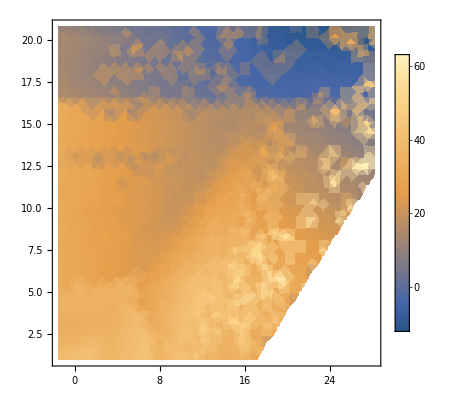

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

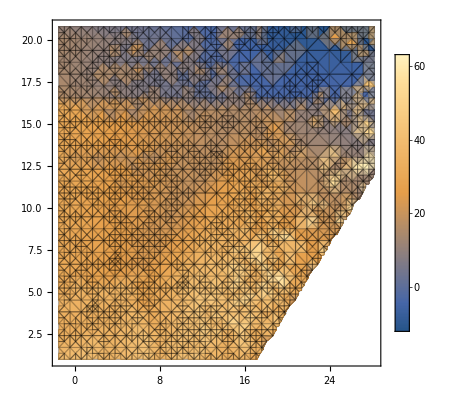

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic,Mesh->All](*0th moment*)
```

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic,Mesh->All,MaxRecursion->5]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic,MaxRecursion->5]
```

-Graphics-

numerical precision 50

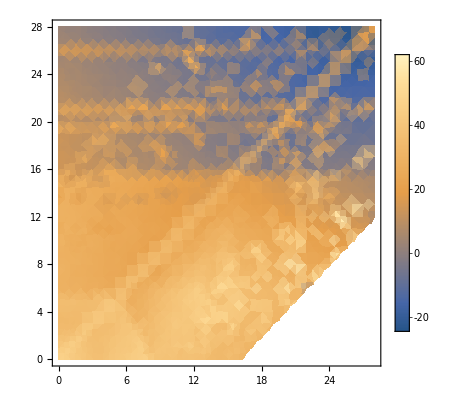

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic]
```

Numerical precision 100

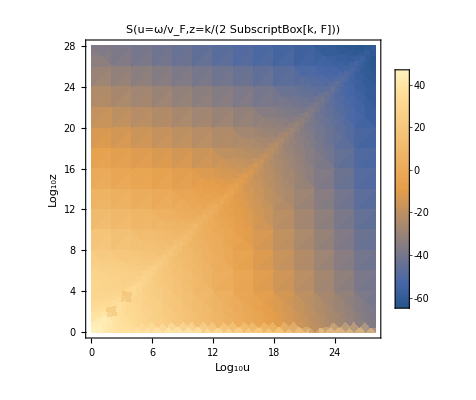

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic,PlotLabel->"S(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

with large z replacement

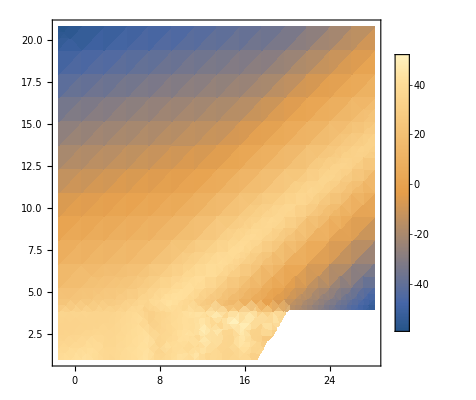

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

Large z and large u

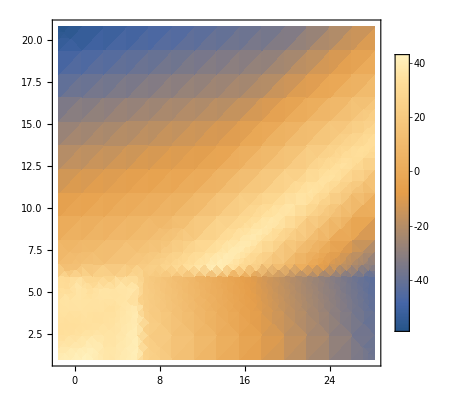

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

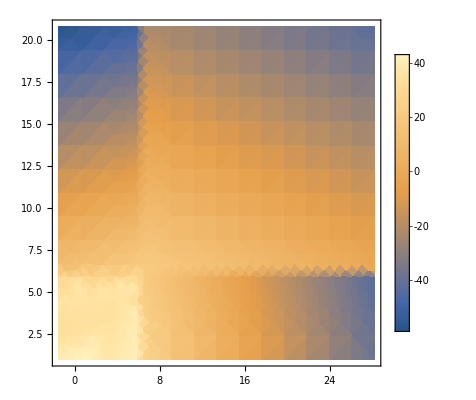

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,-1.5,28.2},{z,1.02,20.8},PlotLegends->Automatic](*0th moment*)
```

10 th order

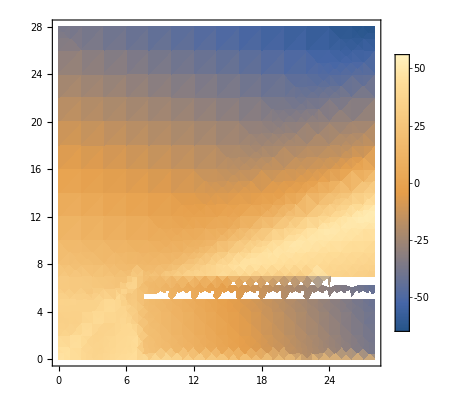

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic,PlotRange->All](*0th moment*)
```

12th

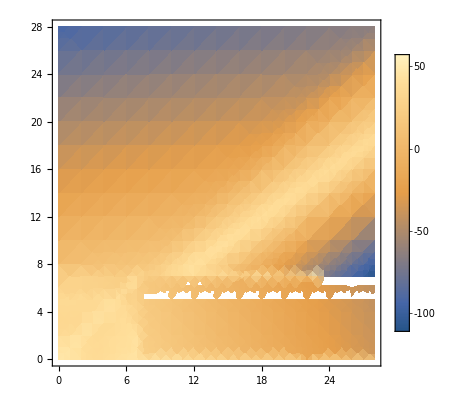

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic](*0th moment*)
```

14th order

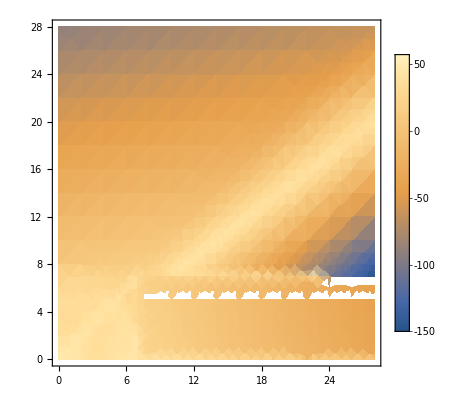

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic](*0th moment*)
```

14th and large u change

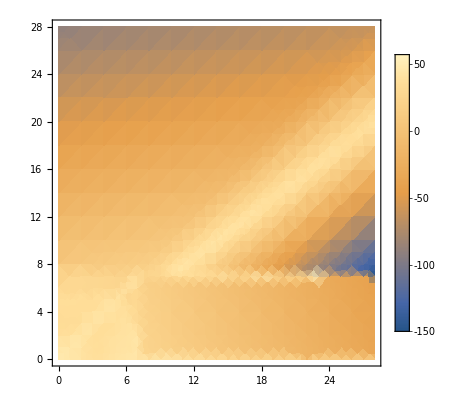

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic](*0th moment*)
```

Just large z at 14th

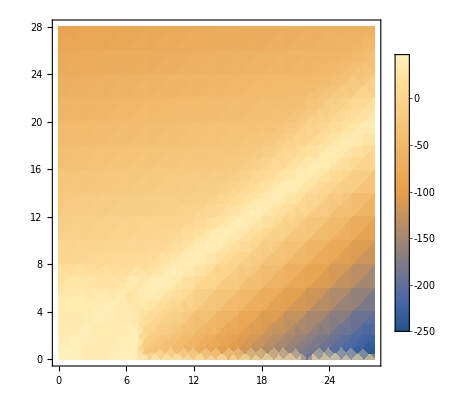

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic](*0th moment*)
```

large z order 8 with uν->uν/z

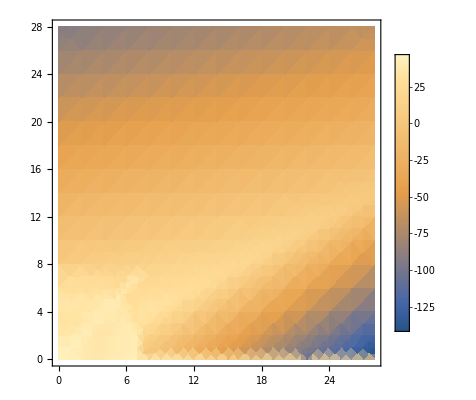

```mathematica
DensityPlot[Log10@StructureFunctionuz[10^u,10^z,FeTotalparams],{u,0,28},{z,0,28},PlotLegends->Automatic](*0th moment*)
```

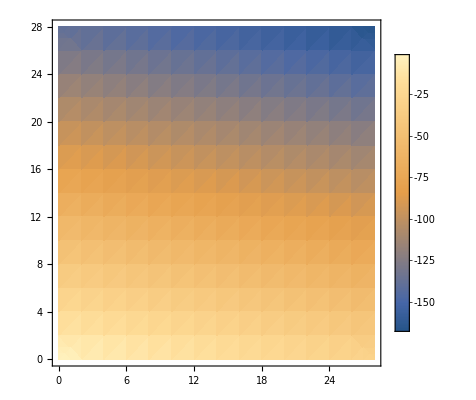

```mathematica
DensityPlot[Log10@(Im[-1/(1+(("χ")^2 (u+ⅈ uν))/(3 z^4 (u-(4 ⅈ uν)/(3 z^2 (-2+z Log[z/Abs[1-z]])))))]/.{"χ"->1,uν->1/z}/.{u->10^ut,z->10^zt}),{ut,0,28},{zt,0,28},PlotLegends->Automatic,PlotRange->All](*0th moment*)
```

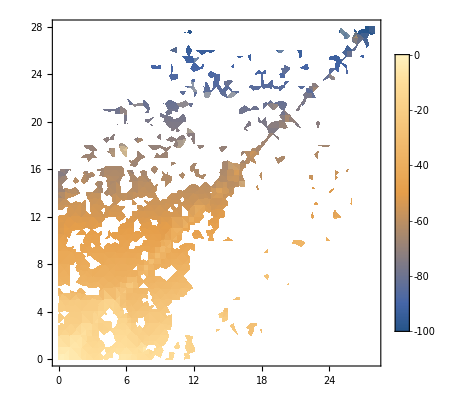

```mathematica
DensityPlot[Log10@Im[-1/N[{1,I}.ϵRPAC[10^u,10^z,10^-1/10^z]/."χ"->1,50]],{u,0,28},{z,0,28},PlotLegends->Automatic,PlotRange->All](*0th moment*)
```

#### Expansions

```mathematica
Im[-1/({1,I}.ϵRPAC[10^u,10^z,10^1/10^z])]
```

-Im[1/(1+ⅈ 2^(-2-3 z) 5^(-3 z) χ^2 (-1/2 (1+10^(2-2 z)-(10^u-10^z)^2) (-ArcTan[10^(-1+z) (1+10^u-10^z)]-ArcTan[10^(-1+z) (1-10^u+10^z)])+1/2 (1+10^(2-2 z)-(10^u+10^z)^2) (-ArcTan[10^(-1+z) (1-10^u-10^z)]-ArcTan[10^(-1+z) (1+10^u+10^z)])-2^-z 5^(1-z) (-10^u+10^z) Log[(10^(2-2 z)+(1+10^u-10^z)^2)/(10^(2-2 z)+(1-10^u+10^z)^2)]+2^-z 5^(1-z) (-10^u-10^z) Log[(10^(2-2 z)+(1+10^u+10^z)^2)/(10^(2-2 z)+(1-10^u-10^z)^2)])+2^(-2-3 z) 5^(-3 z) χ^2 (2^(1+z) 5^z-10^(1-z) (10^u-10^z) (-ArcTan[10^(-1+z) (1+10^u-10^z)]-ArcTan[10^(-1+z) (1-10^u+10^z)])+10^(1-z) (10^u+10^z) (-ArcTan[10^(-1+z) (1-10^u-10^z)]-ArcTan[10^(-1+z) (1+10^u+10^z)])-1/4 (1+10^(2-2 z)-(10^u-10^z)^2) Log[(10^(2-2 z)+(1+10^u-10^z)^2)/(10^(2-2 z)+(1-10^u+10^z)^2)]+1/4 (1+10^(2-2 z)-(10^u+10^z)^2) Log[(10^(2-2 z)+(1+10^u+10^z)^2)/(10^(2-2 z)+(1-10^u-10^z)^2)]))]

```mathematica
1+((1+5 u^2+5 ⅈ u uν) ("χ")^2)/(15 z^6)+("χ")^2/(3 z^4)/."χ"->χ//Simplify
Im[-1/%]//ComplexExpand//Simplify
Series[%,z->∞]
```

1+((1+5 u^2+5 ⅈ u uν) χ^2)/(15 z^6)+χ^2/(3 z^4)

(75 u uν z^6 χ^2)/(25 u^2 uν^2 χ^4+(15 z^6+(1+5 u^2) χ^2+5 z^2 χ^2)^2)

(u uν χ^2)/(3 z^6)+O[1/z]^9

```mathematica
Series[ϵM[u,z,uν],u->∞]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,u->∞]
```

Piecewise[{{1, z≤10000}, {(χ^2 u^2)/(3 z^6)+O[1/u]^2, True}}]

```mathematica
ϵMraw=1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1));
Series[%,{up,∞,5}]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{up,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{up,∞,5}]/.χ->"χ"/.uνt->uν/.up->u//Simplify//Normal
```

1-χ^2/(3 u^2 z^2)+(ⅈ χ^2 uν)/(3 u^3 z^2)-(χ^2 (3-5 uν^2+5 z^2))/(15 u^4 z^2)+(ⅈ χ^2 uν (4 z (17-15 uν^2+45 z^2)-3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(-1+z)^2]+3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(1+z)^2]))/(45 u^5 z^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]))

```mathematica
ϵMraw=1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))%/.uν->uνt/."χ"->χ//Simplify;
ϵMraw/.up->z//Simplify//Normal
```

$Aborted

1+((-13+35 uνt^2) χ^2)/(15 z^6)+(4 ⅈ uνt χ^2)/(3 z^5)-χ^2/z^4+(4 ⅈ uνt χ^2)/(9 z^6 (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]]))

```mathematica
Series[Im[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))],{z,∞,8}]//Normal//Simplify
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,8}]
```

3 Re[(χ^2 (up+ⅈ uν) (3+35 up^4+140 ⅈ up^3 uν+35 uν^4+7 z^2+35 z^4-14 ⅈ up uν (-6+10 uν^2-5 z^2)-7 up^2 (-6+30 uν^2-5 z^2)-7 uν^2 (6+5 z^2)) (-2 z+(-1+z^2) Log[(1+z)/Abs[1-z]]))/(z (2520 ⅈ up uν^6-420 uν^7-630 ⅈ up z^8-1680 ⅈ up uν^4 (3+5 up^2+z^2)+420 uν^5 (3+15 up^2+z^2)+24 ⅈ up uν^2 (45+105 up^4+42 z^2+35 z^4+70 up^2 (3+z^2))-12 uν^3 (45+525 up^4+42 z^2+35 z^4+210 up^2 (3+z^2))+4 uν (5+105 up^6+9 z^2+21 z^4+105 z^6+105 up^4 (3+z^2)+3 up^2 (45+42 z^2+35 z^4))+315 ⅈ up z^7 (-1+z^2) Log[(1+z)/Abs[1-z]]))]

(up uνt χ^2)/(3 z^6)+(2 up (3+5 up^2) uνt χ^2)/(15 z^8)+O[1/z]^9

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1)),{z,∞,8}]//Normal//Simplify;
%/.uν->uνt/."χ"->χ//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,8}]//Simplify//Normal
```

1+((3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) χ^2)/(105 z^8)+((1+5 up^2+5 ⅈ up uνt) χ^2)/(15 z^6)+χ^2/(3 z^4)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->uνt/."χ"->χ,{z,∞,12}]//Normal
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,12}]//Simplify
```

1+χ^2/(3 z^4)+((1+5 up^2+5 ⅈ up uνt) χ^2)/(15 z^6)+((3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) χ^2)/(105 z^8)+((5+105 up^6+315 ⅈ up^5 uνt+up^2 (135-483 uνt^2)-315 up^4 (-1+uνt^2)-21 ⅈ up^3 uνt (-34+5 uνt^2)-3 ⅈ up uνt (-45+28 uνt^2)) χ^2)/(315 z^10)+1/(3465 z^12)(35+1155 up^8+4620 ⅈ up^7 uνt-4620 ⅈ up^5 uνt (-5+uνt^2)-462 up^6 (-14+15 uνt^2)-132 ⅈ up^3 uνt (-127+154 uνt^2)+231 up^4 (30-136 uνt^2+5 uνt^4)+44 ⅈ up uνt (35-66 uνt^2+21 uνt^4)+22 up^2 (70-579 uνt^2+294 uνt^4)) χ^2+O[1/z]^13

```mathematica
1+χ^2/(3 z^4)+((1+5 up^2+5 ⅈ up uνt) χ^2)/(15 z^6)+((3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) χ^2)/(105 z^8)+1/(315 z^10)(5+105 up^6+315 ⅈ up^5 uνt+up^2 (135-483 uνt^2)-315 up^4 (-1+uνt^2)-21 ⅈ up^3 uνt (-34+5 uνt^2)-3 ⅈ up uνt (-45+28 uνt^2)) χ^2+1/(3465 z^12)(35+1155 up^8+4620 ⅈ up^7 uνt-4620 ⅈ up^5 uνt (-5+uνt^2)-462 up^6 (-14+15 uνt^2)-132 ⅈ up^3 uνt (-127+154 uνt^2)+231 up^4 (30-136 uνt^2+5 uνt^4)+44 ⅈ up uνt (35-66 uνt^2+21 uνt^4)+22 up^2 (70-579 uνt^2+294 uνt^4)) χ^2+O[1/z]^13//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

1+1/(3465 z^12)χ^2 (35+1155 u^8+4620 ⅈ u^7 uν-4620 ⅈ u^5 uν (-5+uν^2)-462 u^6 (-14+15 uν^2)-132 ⅈ u^3 uν (-127+154 uν^2)+231 u^4 (30-136 uν^2+5 uν^4)+44 ⅈ u uν (35-66 uν^2+21 uν^4)+22 u^2 (70-579 uν^2+294 uν^4))+(χ^2 (5+105 u^6+315 ⅈ u^5 uν+u^2 (135-483 uν^2)-315 u^4 (-1+uν^2)-21 ⅈ u^3 uν (-34+5 uν^2)-3 ⅈ u uν (-45+28 uν^2)))/(315 z^10)+(χ^2 (3+35 u^4+42 ⅈ u uν+70 ⅈ u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(χ^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+χ^2/(3 z^4)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->uνt/."χ"->χ,{up,∞,6}]//Normal;
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z]->0;
Series[%,{up,∞,6}]//Simplify//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

1-χ^2/(3 u^2 z^2)+(ⅈ χ^2 uν)/(3 u^3 z^2)-(χ^2 (3-5 uν^2+5 z^2))/(15 u^4 z^2)+(ⅈ χ^2 uν (4 z (17-15 uν^2+45 z^2)-3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(-1+z)^2]+3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(1+z)^2]))/(45 u^5 z^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]))-(χ^2 (4 z (35 uν^4-14 uν^2 (4+15 z^2)+5 (3+14 z^2+7 z^4))+(-1+z^2) (35 uν^4-42 uν^2 (3+5 z^2)+5 (3+14 z^2+7 z^4)) Log[(-1+z)^2]-(-1+z^2) (35 uν^4-42 uν^2 (3+5 z^2)+5 (3+14 z^2+7 z^4)) Log[(1+z)^2]))/(105 u^6 z^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]))

```mathematica
1-("χ")^2/(3 u^2 z^2)+(ⅈ ("χ")^2 uν)/(3 u^3 z^2)-(("χ")^2 (3-5 uν^2+5 z^2))/(15 u^4 z^2)+(ⅈ ("χ")^2 uν (4 z (17-15 uν^2+45 z^2)-3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(-1+z)^2]+3 (-9+5 uν^2-15 z^2) (-1+z^2) Log[(1+z)^2]))/(45 u^5 z^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]))-(("χ")^2 (4 z (35 uν^4-14 uν^2 (4+15 z^2)+5 (3+14 z^2+7 z^4))+(-1+z^2) (35 uν^4-42 uν^2 (3+5 z^2)+5 (3+14 z^2+7 z^4)) Log[(-1+z)^2]-(-1+z^2) (35 uν^4-42 uν^2 (3+5 z^2)+5 (3+14 z^2+7 z^4)) Log[(1+z)^2]))/(105 u^6 z^2 (4 z+(-1+z^2) Log[(-1+z)^2]-(-1+z^2) Log[(1+z)^2]));
Series[%,{z,∞,6}]//Simplify//Normal
```

1-(χ^2 (2+u^2-2 ⅈ u uν-3 uν^2))/(3 u^6)+(8 χ^2 uν (ⅈ u+3 uν))/(1125 u^6 z^6)+(8 χ^2 uν (ⅈ u+3 uν))/(525 u^6 z^4)-(χ^2 (15+35 u^4-35 ⅈ u^3 uν-147 uν^2+35 uν^4+35 ⅈ u uν (-2+uν^2)-7 u^2 (-3+5 uν^2)))/(105 u^6 z^2)-(χ^2 z^2)/(3 u^6)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->uνt/."χ"->χ,{z,∞,14}]//Normal;
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,14}]//Simplify//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

1+1/(45045 z^14)χ^2 (315+15015 u^10+75075 ⅈ u^9 uν-30030 ⅈ u^7 uν (-22+5 uν^2)-15015 u^8 (-9+10 uν^2)+3003 ⅈ u^5 uν (350-504 uν^2+5 uν^4)+15015 u^6 (18-90 uν^2+5 uν^4)+286 ⅈ u^3 uν (1322-4203 uν^2+1512 uν^4)+429 u^4 (350-3734 uν^2+2387 uν^4)-13 ⅈ u uν (-1575+5984 uν^2-5412 uν^4+924 uν^6)-13 u^2 (-1575+23518 uν^2-34716 uν^4+8316 uν^6))+1/(3465 z^12)χ^2 (35+1155 u^8+4620 ⅈ u^7 uν-4620 ⅈ u^5 uν (-5+uν^2)-462 u^6 (-14+15 uν^2)-132 ⅈ u^3 uν (-127+154 uν^2)+231 u^4 (30-136 uν^2+5 uν^4)+44 ⅈ u uν (35-66 uν^2+21 uν^4)+22 u^2 (70-579 uν^2+294 uν^4))+(χ^2 (5+105 u^6+315 ⅈ u^5 uν+u^2 (135-483 uν^2)-315 u^4 (-1+uν^2)-21 ⅈ u^3 uν (-34+5 uν^2)-3 ⅈ u uν (-45+28 uν^2)))/(315 z^10)+(χ^2 (3+35 u^4+42 ⅈ u uν+70 ⅈ u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(χ^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+χ^2/(3 z^4)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->uνt/."χ"->χ/.{up->up ϵ,z->z ϵ},{ϵ,∞,16}]//Normal;
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z ϵ]->0;
Series[%,{ϵ,∞,16}]//Simplify//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

$Aborted

$Aborted

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->uνt/."χ"->χ,{z,∞,8}]//Normal;
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,8}]//Simplify//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

1+(χ^2 (3+35 u^4+42 ⅈ u uν+70 ⅈ u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(χ^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+χ^2/(3 z^4)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.uν->ν/z/."χ"->χ,{z,∞,8}]//Normal;
cexpandedlargez=ComplexExpand[%];
cexpandedlargez/.Arg[1+z]->0;
Series[%,{z,∞,8}]//Simplify//Normal;
%/.up->u/.uνt->uν/.χ->"χ"
```

1+(χ^2 (3+42 u^2+35 u^4))/(105 z^8)+(χ^2 (1+5 u^2))/(15 z^6)+χ^2/(3 z^4)+(ⅈ χ^2 u ν)/(3 z^7)

```mathematica
1+(("χ")^2 (3+42 u^2+35 u^4))/(105 z^8)+(("χ")^2 (1+5 u^2))/(15 z^6)+("χ")^2/(3 z^4)+(ⅈ ("χ")^2 u ν)/(3 z^7)/.ν->uν z
```

1+(χ^2 (3+42 u^2+35 u^4))/(105 z^8)+(χ^2 (1+5 u^2))/(15 z^6)+(ⅈ χ^2 u uν)/(3 z^6)+χ^2/(3 z^4)

#### Scrap

```mathematica
Series[ϵM[u ϵ,z ϵ,uν]/.uν->uνt/."χ"->χ,{ϵ,∞,6}]//Normal//Simplify;
Refine[%,Assumptions->{Element[{u,z,uνt,χ,1+z},Reals]}];
cexpandedlargez=ComplexExpand[%]//Simplify;
cexpandedlargez/.Arg[1+z]->0;
Series[%,{ϵ,∞,6}]//Simplify
```

$Aborted

$Aborted

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u ϵ ,z-> z ϵ}/.uν->uνt/."χ"->χ,ϵ->∞]//Normal//Simplify
```

1+((up+ⅈ uνt) χ^2)/(3 z^4 ϵ^4 (up-(4 ⅈ uνt)/(3 z^2 ϵ^2 (-2+z ϵ Log[(z ϵ)/Abs[1-z ϵ]]))))

```mathematica
1+((up+ⅈ uνt) χ^2)/(3 z^4 ϵ^4 (up-(4 ⅈ uνt)/(3 z^2 ϵ^2 (-2+z ϵ Log[(z ϵ)/Abs[1-z ϵ]]))))/.{ϵ->1,uνt->uν,u->up,χ->"χ"}
```

1+(χ^2 (up+ⅈ uν))/(3 z^4 (up-(4 ⅈ uν)/(3 z^2 (-2+z Log[z/Abs[1-z]]))))

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u ,z-> z ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,8}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z ϵ]->0;
Series[%,{ϵ,∞,8}]//Normal//Simplify
```

1/105 (105+((3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) χ^2)/(z^8 ϵ^8)+(7 (1+5 up^2+5 ⅈ up uνt) χ^2)/(z^6 ϵ^6)+(35 χ^2)/(z^4 ϵ^4))

```mathematica
1+1/105 (((3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) χ^2)/(z^8 ϵ^8)+(7 (1+5 up^2+5 ⅈ up uνt) χ^2)/(z^6 ϵ^6)+(35 χ^2)/(z^4 ϵ^4))/.{ϵ->1,uνt->uν,u->up,χ->"χ"}
```

1+1/105 ((χ^2 (3+35 up^4+42 ⅈ up uν+70 ⅈ up^3 uν-7 up^2 (-6+5 uν^2)))/z^8+(7 χ^2 (1+5 up^2+5 ⅈ up uν))/z^6+(35 χ^2)/z^4)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u ,z-> z ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,10}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z ϵ]->0;
Series[%,{ϵ,∞,10}]//Normal//Simplify
```

1/(315 z^10 ϵ^10)(315 z^10 ϵ^10+(5+105 up^6+315 ⅈ up^5 uνt+up^2 (135-483 uνt^2)-315 up^4 (-1+uνt^2)-21 ⅈ up^3 uνt (-34+5 uνt^2)-3 ⅈ up uνt (-45+28 uνt^2)) χ^2+3 (3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) z^2 ϵ^2 χ^2+21 (1+5 up^2+5 ⅈ up uνt) z^4 ϵ^4 χ^2+105 z^6 ϵ^6 χ^2)

```mathematica
1+1/(315 z^10 ϵ^10)((5+105 up^6+315 ⅈ up^5 uνt+up^2 (135-483 uνt^2)-315 up^4 (-1+uνt^2)-21 ⅈ up^3 uνt (-34+5 uνt^2)-3 ⅈ up uνt (-45+28 uνt^2)) χ^2+3 (3+35 up^4+42 ⅈ up uνt+70 ⅈ up^3 uνt-7 up^2 (-6+5 uνt^2)) z^2 ϵ^2 χ^2+21 (1+5 up^2+5 ⅈ up uνt) z^4 ϵ^4 χ^2+105 z^6 ϵ^6 χ^2)/.{ϵ->1,uνt->uν,up->u,χ->"χ"}
```

1+1/(315 z^10)(χ^2 (5+105 u^6+315 ⅈ u^5 uν+u^2 (135-483 uν^2)-315 u^4 (-1+uν^2)-21 ⅈ u^3 uν (-34+5 uν^2)-3 ⅈ u uν (-45+28 uν^2))+3 χ^2 (3+35 u^4+42 ⅈ u uν+70 ⅈ u^3 uν-7 u^2 (-6+5 uν^2)) z^2+21 χ^2 (1+5 u^2+5 ⅈ u uν) z^4+105 χ^2 z^6)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u ,z-> z ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,10}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z ϵ]->0;
Series[%,{ϵ,∞,10}]//Normal//Simplify
```

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u -ϵ,z-> z+ ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,6}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z +ϵ]->0;
Series[%,{ϵ,∞,6}]//Normal//Simplify
```

(15 ϵ^6+(1+5 up^2+5 ⅈ up uνt+50 z^2) χ^2-20 z ϵ χ^2+5 ϵ^2 χ^2)/(15 ϵ^6)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u +ϵ,z-> z- ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,6}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z -ϵ]->0;
Series[%,{ϵ,∞,6}]//Normal//Simplify
```

(15 ϵ^6+(1+5 up^2+5 ⅈ up uνt+50 z^2) χ^2+20 z ϵ χ^2+5 ϵ^2 χ^2)/(15 ϵ^6)

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u +ϵ,z-> z+ ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,6}]//Normal//Simplify;
%//ComplexExpand//Simplify;
%/.Arg[1+z +ϵ]->0;
Series[%,{ϵ,∞,6}]//Normal//Simplify
```

(15 ϵ^6+(1+5 up^2+5 ⅈ up uνt+50 z^2) χ^2-20 z ϵ χ^2+5 ϵ^2 χ^2)/(15 ϵ^6)

```mathematica
1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.up->u;
Series[%,{z,∞,6},{u,∞,6}]//Normal//Simplify
```

$Aborted

```mathematica
Series[ϵRPAC[u,z,uν],{z,∞,6},{u,∞,6}]//Normal//Simplify
```

{1+(χ^2 (1+5 u^2-5 uν^2+5 z^2))/(15 z^6),(2 χ^2 u uν)/(3 z^6)}

```mathematica
ϵRPAC[u,z,uν];
Series[%,{uν,0,0}]//Normal//Simplify;
smalluνϵrpac=%/.√((1+u-z)^2/uν^2)->Abs[(1+u-z)/uν]/.√((1-u+z)^2/uν^2)->Abs[(1-u+z)/uν]/.√((1+u+z)^2/uν^2)->Abs[(1+u+z)/uν]/.√((-1+u+z)^2/uν^2)->Abs[(-1+u+z)/uν]//FullSimplify
(*Series[%,{u,∞,6},{z,∞,6}]//Normal//FullSimplify*)
```

{1/(16 z^3)(8 z (χ^2+2 z^2)+χ^2 ((-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+u+z) (1+u+z) Log[(1+u+z)^2/(-1+u+z)^2])),1/(16 z^3 Abs[uν])χ^2 π uν ((1-u+z) Abs[1+u-z]+(1+u-z) Abs[1-u+z]-(1+u+z) Abs[-1+u+z]+(-1+u+z) Abs[1+u+z])}

```mathematica
((-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+(u+z)^2)Log[(1+u+z)^2/(-1+u+z)^2])//Simplify
```

(-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+(u+z)^2) Log[(1+u+z)^2/(-1+u+z)^2]

```mathematica
ϵRPAC[u,z,uν]
```

{1+1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)]),1/(4 z^3)χ^2 (-1/2 (1+uν^2-(u-z)^2) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+1/2 (1+uν^2-(u+z)^2) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])}

```mathematica
(-1+u+z) (1+u+z)==(u+z)^2-1//Simplify
```

True

```mathematica
Ζtest[a_,uν_]:= Module[{h1,h2},
	(* Used in the Definition of the Mermin Dielectric in the Degenerate Limit
	There's an implicit {1,I} on output ie. [[1]] corresponds to real part and [[2]] corresponds to imaginary part 
	- easier to do this way and keep track of components than deal with refining arctan and logs*)
	h1= -(ArcTan[(1-a)/uν] + ArcTan[(1+a)/uν]);
	h2= 1/2 Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)];
	({a,uν} +{{a uν, 1/2 (1-a^2+uν^2)},{1/2 (1-a^2+uν^2),-a uν}} . {h1,h2})
 ]
```

```mathematica
Ζtest[a,uν]//FullSimplify
```

{a+a uν (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[1+(4 a)/((-1+a)^2+uν^2)],uν+1/2 (-1+a^2-uν^2) (ArcTan[(1-a)/uν]+ArcTan[(1+a)/uν])-1/2 a uν Log[1+(4 a)/((-1+a)^2+uν^2)]}

```mathematica
{a+a uν (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[1+(4 a)/((-1+a)^2+uν^2)],uν+1/2 (-1+a^2-uν^2) (ArcTan[(1-a)/uν]+ArcTan[(1+a)/uν])-1/2 a uν Log[1+(4 a)/((-1+a)^2+uν^2)]}
Series[%,{a,1,3}]
```

{a+a uν (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[1+(4 a)/((-1+a)^2+uν^2)],uν+1/2 (-1+a^2-uν^2) (ArcTan[(1-a)/uν]+ArcTan[(1+a)/uν])-1/2 a uν Log[1+(4 a)/((-1+a)^2+uν^2)]}

{(1-uν ArcTan[2/uν]+1/4 uν^2 Log[1+4/uν^2])+1/2 (4-2 uν ArcTan[2/uν]-Log[1+4/uν^2]) (a-1)+((4-4 Log[1+4/uν^2]-uν^2 Log[1+4/uν^2]) (a-1)^2)/(4 (4+uν^2))-(2 (-4+uν^2) (a-1)^3)/(3 (uν^2 (4+uν^2)^2))+O[a-1]^4,(uν-1/2 uν^2 ArcTan[2/uν]-1/2 uν Log[1+4/uν^2])+1/2 (2 ArcTan[2/uν]-uν Log[1+4/uν^2]) (a-1)+((-4-2 uν^2+4 uν ArcTan[2/uν]+uν^3 ArcTan[2/uν]) (a-1)^2)/(2 uν (4+uν^2))-(8 (a-1)^3)/(3 (uν (4+uν^2)^2))+O[a-1]^4}

```mathematica
smalluνϵrpac/.u->z+ϵ/.uν->1/z//Simplify
```

{(8 z (χ^2+2 z^2)+χ^2 ((-1+ϵ^2) Log[(1+ϵ)^2/(-1+ϵ)^2]-(-1+2 z+ϵ) (1+2 z+ϵ) Log[(1+2 z+ϵ)^2/(-1+2 z+ϵ)^2]))/(16 z^3),(χ^2 π Abs[z] ((1+ϵ) Abs[1-ϵ]-(-1+ϵ) Abs[1+ϵ]-(1+2 z+ϵ) Abs[-1+2 z+ϵ]+(-1+2 z+ϵ) Abs[1+2 z+ϵ]))/(16 z^4)}

```mathematica
N[smalluνϵrpac/.uν->1/z/."χ"->1,50]/.{u->10,z->14}
```

{1.000017911374979764084134791073077261918128437576,0.}

```mathematica
Log10@Im[-1/N[1+{1,I}.smalluνϵrpac/.uν->1/z/."χ"->1,50]]/.z->zt/.u->zt+ϵ/.uν->1/zt/.{zt->1,ϵ->0.4}
```

-1.04453

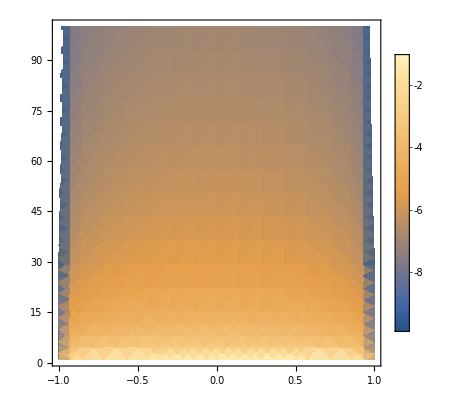

```mathematica
DensityPlot[Log10@Im[-1/N[1+{1,I}.smalluνϵrpac/.uν->1/z/."χ"->1,50]]/.z->zt/.u->zt+ϵ/.uν->1/zt,{ϵ,-1,1},{zt,1,100},PlotLegends->Automatic](*0th moment*)
```

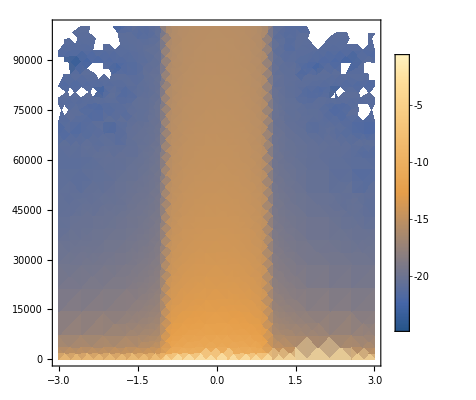

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.z->zt/.u->zt+ϵ/.uν->1/zt,{ϵ,-3,3},{zt,1,10^5},PlotLegends->Automatic](*0th moment*)
```

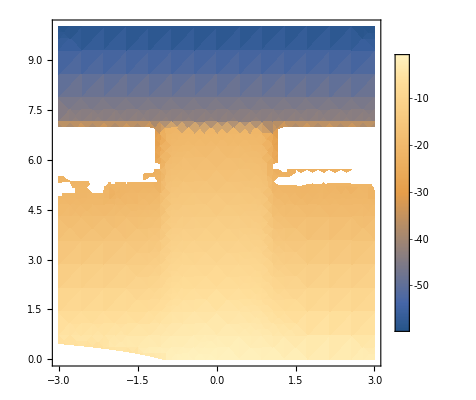

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.z->10^zt/.u->10^zt+ϵ/.uν->1/zt,{ϵ,-3,3},{zt,0,10},PlotLegends->Automatic]
```

```mathematica
ϵRPAC[u,z,uν];
Series[%,{uν,0,1}]//Normal//Simplify;
smalluνϵrpac1=%/.√((1+u-z)^2/uν^2)->Abs[(1+u-z)/uν]/.√((1-u+z)^2/uν^2)->Abs[(1-u+z)/uν]/.√((1+u+z)^2/uν^2)->Abs[(1+u+z)/uν]/.√((-1+u+z)^2/uν^2)->Abs[(-1+u+z)/uν]//FullSimplify
```

{1/(16 z^3 Sign[-1+u+z])(((-1+u+z) (-2 χ^2 π uν (u-z) Abs[uν] (√((-1+u-z) (-1+Conjugate[u]-Conjugate[z]))+(√((-1+u-z) (-1+Conjugate[u]-Conjugate[z]))-√((1+u-z) (1+Conjugate[u]-Conjugate[z]))) (Conjugate[u]-Conjugate[z])+√((1+u-z) (1+Conjugate[u]-Conjugate[z])))-Conjugate[uν] √((-1+u-z) (-1+Conjugate[u]-Conjugate[z])) √((1+u-z) (1+Conjugate[u]-Conjugate[z])) (8 z (χ^2+2 z^2)+χ^2 ((-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+u+z) (1+u+z) Log[(1+u+z)^2/(-1+u+z)^2]))))/(Conjugate[uν] (-1+(Conjugate[u]-Conjugate[z])^2) √((-1+u+z) (-1+Conjugate[u]+Conjugate[z])) Sign[1+u-z] Sign[1-u+z])-(2 χ^2 π uν (u+z) Sign[uν] (Sign[-1+u+z]-Sign[1+u+z]))/Sign[1+u+z]),1/(16 z^3 Abs[uν])χ^2 uν (π (1-u+z) Abs[1+u-z]+π (1+u-z) Abs[1-u+z]-π Abs[-1+u+z]-π u Abs[-1+u+z]-π z Abs[-1+u+z]-π Abs[1+u+z]+π u Abs[1+u+z]+π z Abs[1+u+z]+2 u Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 z Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 (u+z) Abs[uν] Log[(1+u+z)^2/(-1+u+z)^2])}

```mathematica
{1/(16 z^3 Sign[-1+u+z])(((-1+u+z) (-2 ("χ")^2 π uν (u-z) Abs[uν] (√((-1+u-z) (-1+Conjugate[u]-Conjugate[z]))+(√((-1+u-z) (-1+Conjugate[u]-Conjugate[z]))-√((1+u-z) (1+Conjugate[u]-Conjugate[z]))) (Conjugate[u]-Conjugate[z])+√((1+u-z) (1+Conjugate[u]-Conjugate[z])))-Conjugate[uν] √((-1+u-z) (-1+Conjugate[u]-Conjugate[z])) √((1+u-z) (1+Conjugate[u]-Conjugate[z])) (8 z (("χ")^2+2 z^2)+("χ")^2 ((-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+u+z) (1+u+z) Log[(1+u+z)^2/(-1+u+z)^2]))))/(Conjugate[uν] (-1+(Conjugate[u]-Conjugate[z])^2) √((-1+u+z) (-1+Conjugate[u]+Conjugate[z])) Sign[1+u-z] Sign[1-u+z])-(2 ("χ")^2 π uν (u+z) Sign[uν] (Sign[-1+u+z]-Sign[1+u+z]))/Sign[1+u+z]),1/(16 z^3 Abs[uν])("χ")^2 uν (π (1-u+z) Abs[1+u-z]+π (1+u-z) Abs[1-u+z]-π Abs[-1+u+z]-π u Abs[-1+u+z]-π z Abs[-1+u+z]-π Abs[1+u+z]+π u Abs[1+u+z]+π z Abs[1+u+z]+2 u Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 z Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 (u+z) Abs[uν] Log[(1+u+z)^2/(-1+u+z)^2])}/.Conjugate[z]->z/.Conjugate[u]->u
```

{1/(16 z^3 Sign[-1+u+z])(((-1+u+z) (-2 χ^2 π uν (√((-1+u-z)^2)+(√((-1+u-z)^2)-√((1+u-z)^2)) (u-z)+√((1+u-z)^2)) (u-z) Abs[uν]-√((-1+u-z)^2) √((1+u-z)^2) Conjugate[uν] (8 z (χ^2+2 z^2)+χ^2 ((-1+(u-z)^2) Log[(1+u-z)^2/(1-u+z)^2]-(-1+u+z) (1+u+z) Log[(1+u+z)^2/(-1+u+z)^2]))))/((-1+(u-z)^2) √((-1+u+z)^2) Conjugate[uν] Sign[1+u-z] Sign[1-u+z])-(2 χ^2 π uν (u+z) Sign[uν] (Sign[-1+u+z]-Sign[1+u+z]))/Sign[1+u+z]),1/(16 z^3 Abs[uν])χ^2 uν (π (1-u+z) Abs[1+u-z]+π (1+u-z) Abs[1-u+z]-π Abs[-1+u+z]-π u Abs[-1+u+z]-π z Abs[-1+u+z]-π Abs[1+u+z]+π u Abs[1+u+z]+π z Abs[1+u+z]+2 u Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 z Abs[uν] Log[(1+u-z)^2/(1-u+z)^2]-2 (u+z) Abs[uν] Log[(1+u+z)^2/(-1+u+z)^2])}

```mathematica
Im[-1/N[{1,I}.smalluνϵrpac/.uν->1/z/."χ"->1,50]/.{u->10^1,z->10^9}]
```

0.

```mathematica
1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u -ϵ,z-> z+ ϵ}/.uν->uνt/."χ"->χ
```

1+((up+ⅈ uνt) (1/(4 (z+ϵ)^3)ⅈ χ^2 (-1/2 (1+uνt^2-(up-z-ϵ)^2) (-ArcTan[(1+up-z-ϵ)/uνt]-ArcTan[(1-up+z+ϵ)/uνt])+1/2 (1+uνt^2-(up+z+ϵ)^2) (-ArcTan[(1-up-z-ϵ)/uνt]-ArcTan[(1+up+z+ϵ)/uνt])-1/2 uνt (-up+z+ϵ) Log[(uνt^2+(1+up-z-ϵ)^2)/(uνt^2+(1-up+z+ϵ)^2)]+1/2 uνt (-up-z-ϵ) Log[(uνt^2+(1+up+z+ϵ)^2)/(uνt^2+(1-up-z-ϵ)^2)])+1/(4 (z+ϵ)^3)χ^2 (2 (z+ϵ)-uνt (up-z-ϵ) (-ArcTan[(1+up-z-ϵ)/uνt]-ArcTan[(1-up+z+ϵ)/uνt])+uνt (up+z+ϵ) (-ArcTan[(1-up-z-ϵ)/uνt]-ArcTan[(1+up+z+ϵ)/uνt])-1/4 (1+uνt^2-(up-z-ϵ)^2) Log[(uνt^2+(1+up-z-ϵ)^2)/(uνt^2+(1-up+z+ϵ)^2)]+1/4 (1+uνt^2-(up+z+ϵ)^2) Log[(uνt^2+(1+up+z+ϵ)^2)/(uνt^2+(1-up-z-ϵ)^2)])))/(up+1/(χ^2 (1/2+((1-(z+ϵ)^2) Log[(1+z+ϵ)/Abs[1-z-ϵ]])/(4 (z+ϵ))))ⅈ uνt (z+ϵ)^2 (1/(4 (z+ϵ)^3)ⅈ χ^2 (-1/2 (1+uνt^2-(up-z-ϵ)^2) (-ArcTan[(1+up-z-ϵ)/uνt]-ArcTan[(1-up+z+ϵ)/uνt])+1/2 (1+uνt^2-(up+z+ϵ)^2) (-ArcTan[(1-up-z-ϵ)/uνt]-ArcTan[(1+up+z+ϵ)/uνt])-1/2 uνt (-up+z+ϵ) Log[(uνt^2+(1+up-z-ϵ)^2)/(uνt^2+(1-up+z+ϵ)^2)]+1/2 uνt (-up-z-ϵ) Log[(uνt^2+(1+up+z+ϵ)^2)/(uνt^2+(1-up-z-ϵ)^2)])+1/(4 (z+ϵ)^3)χ^2 (2 (z+ϵ)-uνt (up-z-ϵ) (-ArcTan[(1+up-z-ϵ)/uνt]-ArcTan[(1-up+z+ϵ)/uνt])+uνt (up+z+ϵ) (-ArcTan[(1-up-z-ϵ)/uνt]-ArcTan[(1+up+z+ϵ)/uνt])-1/4 (1+uνt^2-(up-z-ϵ)^2) Log[(uνt^2+(1+up-z-ϵ)^2)/(uνt^2+(1-up+z+ϵ)^2)]+1/4 (1+uνt^2-(up+z+ϵ)^2) Log[(uνt^2+(1+up+z+ϵ)^2)/(uνt^2+(1-up-z-ϵ)^2)])))

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u -ϵ,z-> z+ ϵ}/.uν->uνt/."χ"->χ,{ϵ,0,0}]//Normal;
%//ComplexExpand;
%/.Arg[1+z +ϵ]->0;
Series[%,{ϵ,0,0}]//Normal//Simplify
```

$Aborted

```mathematica
Series[1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.{u->u ϵ,z-> z ϵ}/.uν->uνt/."χ"->χ,{ϵ,∞,6}]//Normal;
%//ComplexExpand;
%/.Arg[1+z ϵ]->0;
Series[%,{ϵ,∞,6}]//Normal//Simplify
```

1+((1+5 up^2+5 ⅈ up uνt) χ^2)/(15 z^6 ϵ^6)+χ^2/(3 z^4 ϵ^4)

1+(χ^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+χ^2/(3 z^4)

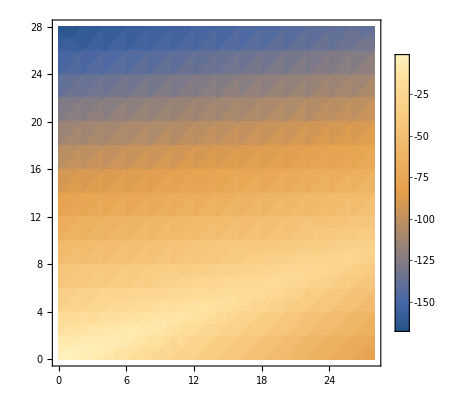

```mathematica
1+((1+5 up^2+5 ⅈ up uνt) χ^2)/(15 z^6 ϵ^6)+χ^2/(3 z^4 ϵ^4)/.χ->"χ"/.uνt->uν/.up->u/.ϵ->1
DensityPlot[Log10@(Im[-1/%]/.{"χ"->1,uν->1}/.{u->10^ut,z->10^zt}),{ut,0,28},{zt,0,28},PlotLegends->Automatic,PlotRange->All](*0th moment*)
```

```mathematica
ϵRPAC[u,z,uν][[1]]
```

1+1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])

```mathematica
ϵRPAC[u,z,x][[1]]
Series[%,{x,0,1}]//Simplify
```

1+1/(4 z^3)χ^2 (2 z-x (u-z) (-ArcTan[(1+u-z)/x]-ArcTan[(1-u+z)/x])+x (u+z) (-ArcTan[(1-u-z)/x]-ArcTan[(1+u+z)/x])-1/4 (1+x^2-(u-z)^2) Log[(x^2+(1+u-z)^2)/(x^2+(1-u+z)^2)]+1/4 (1+x^2-(u+z)^2) Log[(x^2+(1+u+z)^2)/(x^2+(1-u-z)^2)])

1/(16 z^3)(8 χ^2 z+16 z^3-χ^2 Log[(1+u-z)^2/(1-u+z)^2]+χ^2 u^2 Log[(1+u-z)^2/(1-u+z)^2]-2 χ^2 u z Log[(1+u-z)^2/(1-u+z)^2]+χ^2 z^2 Log[(1+u-z)^2/(1-u+z)^2]+χ^2 Log[(1+u+z)^2/(-1+u+z)^2]-χ^2 u^2 Log[(1+u+z)^2/(-1+u+z)^2]-2 χ^2 u z Log[(1+u+z)^2/(-1+u+z)^2]-χ^2 z^2 Log[(1+u+z)^2/(-1+u+z)^2])-((χ^2 π x (-u √((-1+u-z)^2/x^2)-u^2 √((-1+u-z)^2/x^2)+u^3 √((-1+u-z)^2/x^2)+u^4 √((-1+u-z)^2/x^2)-u √((1+u-z)^2/x^2)+u^2 √((1+u-z)^2/x^2)+u^3 √((1+u-z)^2/x^2)-u^4 √((1+u-z)^2/x^2)+√((-1+u-z)^2/x^2) z+2 u √((-1+u-z)^2/x^2) z+u^2 √((-1+u-z)^2/x^2) z+√((1+u-z)^2/x^2) z-2 u √((1+u-z)^2/x^2) z+u^2 √((1+u-z)^2/x^2) z-√((-1+u-z)^2/x^2) z^2-u √((-1+u-z)^2/x^2) z^2-2 u^2 √((-1+u-z)^2/x^2) z^2+√((1+u-z)^2/x^2) z^2-u √((1+u-z)^2/x^2) z^2+2 u^2 √((1+u-z)^2/x^2) z^2-√((-1+u-z)^2/x^2) z^3-√((1+u-z)^2/x^2) z^3+√((-1+u-z)^2/x^2) z^4-√((1+u-z)^2/x^2) z^4+u √((-1+u+z)^2/x^2)+u^2 √((-1+u+z)^2/x^2)-u^3 √((-1+u+z)^2/x^2)-u^4 √((-1+u+z)^2/x^2)+z √((-1+u+z)^2/x^2)+2 u z √((-1+u+z)^2/x^2)+u^2 z √((-1+u+z)^2/x^2)+z^2 √((-1+u+z)^2/x^2)+u z^2 √((-1+u+z)^2/x^2)+2 u^2 z^2 √((-1+u+z)^2/x^2)-z^3 √((-1+u+z)^2/x^2)-z^4 √((-1+u+z)^2/x^2)+u √((1+u+z)^2/x^2)-u^2 √((1+u+z)^2/x^2)-u^3 √((1+u+z)^2/x^2)+u^4 √((1+u+z)^2/x^2)+z √((1+u+z)^2/x^2)-2 u z √((1+u+z)^2/x^2)+u^2 z √((1+u+z)^2/x^2)-z^2 √((1+u+z)^2/x^2)+u z^2 √((1+u+z)^2/x^2)-2 u^2 z^2 √((1+u+z)^2/x^2)-z^3 √((1+u+z)^2/x^2)+z^4 √((1+u+z)^2/x^2))) x)/(8 ((-1+u-z) (1+u-z) z^3 (-1+u+z) (1+u+z)))+O[x]^2

```mathematica
Series[Log[1+x] ,{x,0,1}]
```

x+O[x]^2

#### Look for analytic formula for the expansion

```mathematica
ϵRPAC[u,z,uν]
```

{1+1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)]),1/(4 z^3)χ^2 (-1/2 (1+uν^2-(u-z)^2) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+1/2 (1+uν^2-(u+z)^2) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])}

```mathematica
D[1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)],{z,n}]
```

1/4 (Piecewise[{{n! (1/n(1-u^2+uν^2+2 u z-z^2) (-2 (-(ⅈ ((-1+u-ⅈ uν-z)^-n-(-1+u+ⅈ uν-z)^-n) (1-u+z))/(2 uν)+(Piecewise[{{-(ⅈ ((-1+u-ⅈ uν-z)^(1-n)-(-1+u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}]))+2 (-(ⅈ ((1+u-ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n) (-1-u+z))/(2 uν)+(Piecewise[{{-(ⅈ ((1+u-ⅈ uν-z)^(1-n)-(1+u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])))-(Piecewise[{{Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)], -2+n==0}, {1/(-2+n)(-2 ((1-u+z) (Piecewise[{{-(ⅈ ((-1+u-ⅈ uν-z)^(2-n)-(-1+u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((-1+u-ⅈ uν-z)^(3-n)-(-1+u+ⅈ uν-z)^(3-n)))/(2 uν), -4+n≥0}, {0, True}}]))+2 ((-1-u+z) (Piecewise[{{-(ⅈ ((1+u-ⅈ uν-z)^(2-n)-(1+u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((1+u-ⅈ uν-z)^(3-n)-(1+u+ⅈ uν-z)^(3-n)))/(2 uν), -4+n≥0}, {0, True}}]))), True}}])+(2 u-2 z) (Piecewise[{{Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)], -1+n==0}, {1/(-1+n)(-2 ((1-u+z) (Piecewise[{{-(ⅈ ((-1+u-ⅈ uν-z)^(1-n)-(-1+u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((-1+u-ⅈ uν-z)^(2-n)-(-1+u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}]))+2 ((-1-u+z) (Piecewise[{{-(ⅈ ((1+u-ⅈ uν-z)^(1-n)-(1+u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((1+u-ⅈ uν-z)^(2-n)-(1+u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}]))), True}}])), n≥1}, {(1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)], True}}])+1/4 (Piecewise[{{n! (1/n(1-u^2+uν^2-2 u z-z^2) (2 (-(ⅈ ((-1-u-ⅈ uν-z)^-n-(-1-u+ⅈ uν-z)^-n) (1+u+z))/(2 uν)+(Piecewise[{{-(ⅈ ((-1-u-ⅈ uν-z)^(1-n)-(-1-u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}]))-2 (-(ⅈ ((1-u-ⅈ uν-z)^-n-(1-u+ⅈ uν-z)^-n) (-1+u+z))/(2 uν)+(Piecewise[{{-(ⅈ ((1-u-ⅈ uν-z)^(1-n)-(1-u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])))-(Piecewise[{{Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)], -2+n==0}, {1/(-2+n)(2 ((1+u+z) (Piecewise[{{-(ⅈ ((-1-u-ⅈ uν-z)^(2-n)-(-1-u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((-1-u-ⅈ uν-z)^(3-n)-(-1-u+ⅈ uν-z)^(3-n)))/(2 uν), -4+n≥0}, {0, True}}]))-2 ((-1+u+z) (Piecewise[{{-(ⅈ ((1-u-ⅈ uν-z)^(2-n)-(1-u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((1-u-ⅈ uν-z)^(3-n)-(1-u+ⅈ uν-z)^(3-n)))/(2 uν), -4+n≥0}, {0, True}}]))), True}}])+(-2 u-2 z) (Piecewise[{{Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)], -1+n==0}, {1/(-1+n)(2 ((1+u+z) (Piecewise[{{-(ⅈ ((-1-u-ⅈ uν-z)^(1-n)-(-1-u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((-1-u-ⅈ uν-z)^(2-n)-(-1-u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}]))-2 ((-1+u+z) (Piecewise[{{-(ⅈ ((1-u-ⅈ uν-z)^(1-n)-(1-u+ⅈ uν-z)^(1-n)))/(2 uν), -2+n≥0}, {0, True}}])+(Piecewise[{{-(ⅈ ((1-u-ⅈ uν-z)^(2-n)-(1-u+ⅈ uν-z)^(2-n)))/(2 uν), -3+n≥0}, {0, True}}]))), True}}])), n≥1}, {(1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)], True}}])

```mathematica
D[1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)],{z,n}]
Limit[%,z->∞]
```

1/2 uν (Piecewise[{{n! (Piecewise[{{1/((-1+n) n uν)ⅈ (-ⅈ (1-n) uν ((-1+u-ⅈ uν-z)^-n-(1+u-ⅈ uν-z)^-n+(-1+u+ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n) (u-z)+n ((1+u-ⅈ uν-z)^(1-n)-(1+u+ⅈ uν-z)^(1-n)) (1+u-z)+n ((-1+u-ⅈ uν-z)^(1-n)-(-1+u+ⅈ uν-z)^(1-n)) (1-u+z)), 2≤n<3}, {-(ⅈ (-u+z) (((1+u-ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n) (-1-u+z)-((-1+u-ⅈ uν-z)^-n-(-1+u+ⅈ uν-z)^-n) (1-u+z)))/(n uν), 1<n<2}, {1/((-1+n) n)ⅈ (n (uν (-(-1+u-ⅈ uν-z)^-n+(1+u-ⅈ uν-z)^-n+(-1+u+ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n)+ⅈ ((-1+u-ⅈ uν-z)^-n+(1+u-ⅈ uν-z)^-n+(-1+u+ⅈ uν-z)^-n+(1+u+ⅈ uν-z)^-n))-ⅈ (u ((-1+u-ⅈ uν-z)^-n-(1+u-ⅈ uν-z)^-n+(-1+u+ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n)+(-(-1+u-ⅈ uν-z)^-n+(1+u-ⅈ uν-z)^-n-(-1+u+ⅈ uν-z)^-n+(1+u+ⅈ uν-z)^-n) z)), n≥3}, {-(ⅈ (u-z) (((1+u-ⅈ uν-z)^-n-(1+u+ⅈ uν-z)^-n) (1+u-z)+((-1+u-ⅈ uν-z)^-n-(-1+u+ⅈ uν-z)^-n) (1-u+z)))/(n uν)+Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)], True}}]), n≥1}, {(-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)], True}}])+1/2 uν (Piecewise[{{n! (Piecewise[{{(ⅈ (-u-z) (((1-u-ⅈ uν-z)^-n-(1-u+ⅈ uν-z)^-n) (-1+u+z)-((-1-u-ⅈ uν-z)^-n-(-1-u+ⅈ uν-z)^-n) (1+u+z)))/(n uν), 1<n<2}, {(((-1-u-ⅈ uν-z)^-n-(1-u-ⅈ uν-z)^-n+(-1-u+ⅈ uν-z)^-n-(1-u+ⅈ uν-z)^-n) (u+z))/n-(ⅈ (((1-u-ⅈ uν-z)^(1-n)-(1-u+ⅈ uν-z)^(1-n)) (1-u-z)+((-1-u-ⅈ uν-z)^(1-n)-(-1-u+ⅈ uν-z)^(1-n)) (1+u+z)))/(uν-n uν), 2≤n<3}, {(((-1-u-ⅈ uν-z)^-n-(1-u-ⅈ uν-z)^-n+(-1-u+ⅈ uν-z)^-n-(1-u+ⅈ uν-z)^-n) (u+z))/n-1/(uν-n uν)ⅈ (((1-u-ⅈ uν-z)^(1-n)-(1-u+ⅈ uν-z)^(1-n)) (1-u-z)+(-1-u-ⅈ uν-z)^(2-n)-(1-u-ⅈ uν-z)^(2-n)-(-1-u+ⅈ uν-z)^(2-n)+(1-u+ⅈ uν-z)^(2-n)+((-1-u-ⅈ uν-z)^(1-n)-(-1-u+ⅈ uν-z)^(1-n)) (1+u+z)), n≥3}, {(ⅈ (u+z) (((1-u-ⅈ uν-z)^-n-(1-u+ⅈ uν-z)^-n) (1-u-z)+((-1-u-ⅈ uν-z)^-n-(-1-u+ⅈ uν-z)^-n) (1+u+z)))/(n uν)-Log[(uν^2+(1+u+z)^2)/(uν^2+(-1+u+z)^2)], True}}]), n≥1}, {(-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)], True}}])

$Aborted

```mathematica
order = 2;
D[Ζtest[a,uν]-Ζtest[u-z,uν/z],{z,order}];
Limit[z^(2 order)/(order!)%,z->∞]
```

{∞,0}

```mathematica
4!
```

24

{2/(3 a)+O[1/a]^3,-(2 uν)/(3 a^2)+O[1/a]^3}

{2/(3 a),-(2 uν)/(3 a^2)}

{(4 z)/(3 (-u^2+z^2)),(8 u uν z)/(3 (u-z)^2 (u+z)^2)}

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

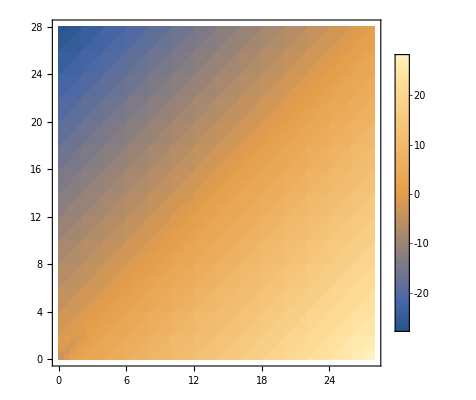

```mathematica
Series[Ζtest[a,uν],{a,∞,2}]
largea=%//Normal
(%/.a->(u+z))-(%/.a->(u-z))//Simplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic](*0th moment*)
```

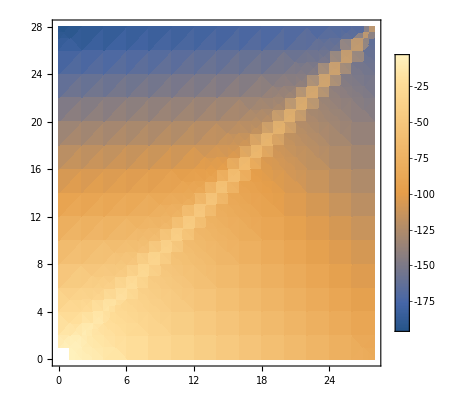

```mathematica
DensityPlot[Log10@Im[-1/({1,I}.ϵRPAC[u,z,uν]/.uν->1/z/."χ"->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

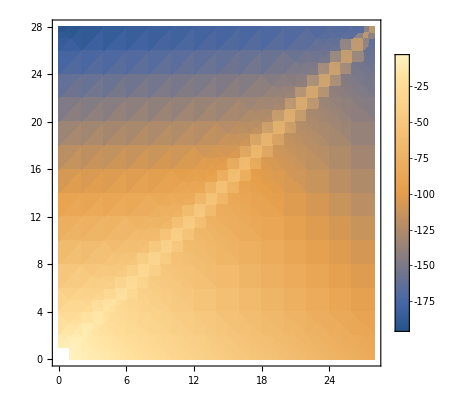

```mathematica
DensityPlot[Log10@Im[-1/(ϵM[u,z,uν]/.uν->1/z/."χ"->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

```mathematica
DensityPlot[Log10@Im[-1/(ϵM[u,z,uν]/.uν->1/z/."χ"->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

-Graphics-

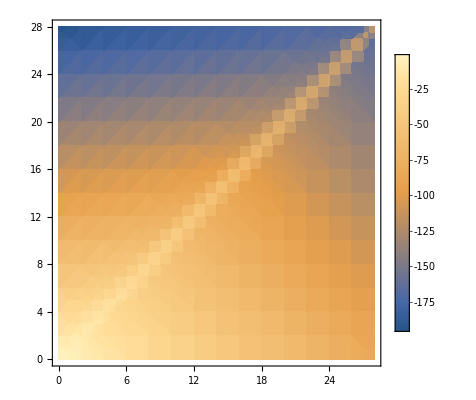

```mathematica
DensityPlot[Log10@Im[-1/({1,I}.ϵRPAC[u,z,uν]/.uν->1/z/."χ"->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

{-1/(315 (u+z))(-210-10 u^10+80 u^9 z+315 (-2+π uν) z^2+210 z^4+42 z^6+18 z^8+10 z^10+84 u^5 z (2+3 z^2)-18 u^8 (1+15 z^2)+12 u^7 z (9+40 z^2)-42 u^6 (1+6 z^2+10 z^4)+210 u^4 (-1-z^2+2 z^6)-4 u z^3 (105+42 z^2+27 z^4+20 z^6)-12 u^3 z (-35+21 z^4+40 z^6)+3 u^2 (210-105 π uν+70 z^4+84 z^6+90 z^8)),-1/2 π (-1+u^2-2 u z+z^2)+1/(315 (u+z)^2)2 uν (-105+35 u^12-280 u^11 z-315 z^2+315 z^4+105 z^6+63 z^8+45 z^10+35 z^12-10 u^9 z (27+140 z^2)+5 u^10 (9+182 z^2)+12 u^7 z (-21-30 z^2+140 z^4)+u^8 (63+585 z^2+525 z^4)+42 u^5 z (-5+6 z^2+30 z^4+40 z^6)-21 u^6 (-5-12 z^2+30 z^4+140 z^6)-4 u^3 z^3 (-105-63 z^2+90 z^4+350 z^6)+105 u^4 (3-z^2-6 z^4-6 z^6+5 z^8)-2 u z (315+105 z^4+126 z^6+135 z^8+140 z^10)+u^2 (-315-630 z^2-105 z^4+252 z^6+585 z^8+910 z^10))}

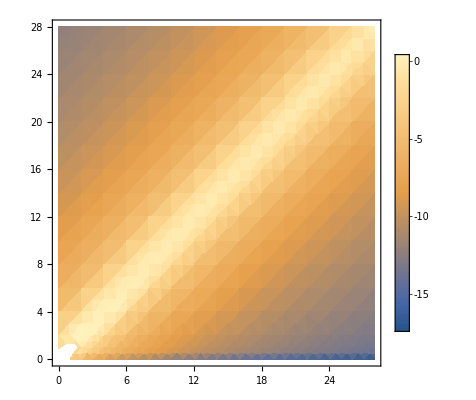

```mathematica
Series[Ζtest[a,uν],{a,0,10}];
smalla=%//Normal;
(largea/.a->(u+z))-(smalla/.a->(u-z))//Simplify;
Series[%,{uν,0,1}]//PowerExpand//Normal//Simplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1/z)],{u,0,28},{z,0,28},PlotLegends->Automatic,PlotRange->All]
```

```mathematica
{-1/(315 (u+z))(-210-10 u^10+80 u^9 z+315 (-2+π uν) z^2+210 z^4+42 z^6+18 z^8+10 z^10+84 u^5 z (2+3 z^2)-18 u^8 (1+15 z^2)+12 u^7 z (9+40 z^2)-42 u^6 (1+6 z^2+10 z^4)+210 u^4 (-1-z^2+2 z^6)-4 u z^3 (105+42 z^2+27 z^4+20 z^6)-12 u^3 z (-35+21 z^4+40 z^6)+3 u^2 (210-105 π uν+70 z^4+84 z^6+90 z^8)),-1/2 π (-1+u^2-2 u z+z^2)+1/(315 (u+z)^2)2 uν (-105+35 u^12-280 u^11 z-315 z^2+315 z^4+105 z^6+63 z^8+45 z^10+35 z^12-10 u^9 z (27+140 z^2)+5 u^10 (9+182 z^2)+12 u^7 z (-21-30 z^2+140 z^4)+u^8 (63+585 z^2+525 z^4)+42 u^5 z (-5+6 z^2+30 z^4+40 z^6)-21 u^6 (-5-12 z^2+30 z^4+140 z^6)-4 u^3 z^3 (-105-63 z^2+90 z^4+350 z^6)+105 u^4 (3-z^2-6 z^4-6 z^6+5 z^8)-2 u z (315+105 z^4+126 z^6+135 z^8+140 z^10)+u^2 (-315-630 z^2-105 z^4+252 z^6+585 z^8+910 z^10))}//FullSimplify
```

{1/315 (315 (-2+π uν)+210 (u-z)^2+42 (u-z)^4+2 (9+5 (u-z)^2) (u-z)^6) (u-z)+2/(3 (u+z)),-2 uν-1/2 π (-1+(u-z)^2)+2 uν (u-z)^2+2/3 uν (u-z)^4+2/5 uν (u-z)^6+2/63 uν (9+7 (u-z)^2) (u-z)^8-(2 uν)/(3 (u+z)^2)}

{-1/(45045 (u+z))(-30030-630 u^14+7560 u^13 z+45045 (-2+π uν) z^2+30030 z^4+6006 z^6+2574 z^8+1430 z^10+910 z^12+630 z^14-910 u^12 (1+45 z^2)+1820 u^11 z (5+72 z^2)+1716 u^7 z (9+40 z^2+70 z^4)+2860 u^9 z (4+35 z^2+126 z^4)-1430 u^10 (1+28 z^2+189 z^4)-858 u^8 (3+45 z^2+175 z^4+315 z^6)-12012 u^5 z (-2-3 z^2+10 z^6+30 z^8)+6006 u^6 (-1-6 z^2-10 z^4+45 z^8)+30030 u^4 (-1-z^2+2 z^6+5 z^8+9 z^10)-4 u z^3 (15015+6006 z^2+3861 z^4+2860 z^6+2275 z^8+1890 z^10)-52 u^3 z (-1155+693 z^4+1320 z^6+1925 z^8+2520 z^10)+13 u^2 (6930-3465 π uν+2310 z^4+2772 z^6+2970 z^8+3080 z^10+3150 z^12)),-1/2 π (-1+u^2-2 u z+z^2)+1/(45045 (u+z)^2)2 uν (-15015+3465 u^16-41580 u^15 z-45045 z^2+45045 z^4+15015 z^6+9009 z^8+6435 z^10+5005 z^12+4095 z^14+3465 z^16+315 u^14 (13+704 z^2)-630 u^13 z (65+1078 z^2)+715 u^10 (9+182 z^2+693 z^4)-1820 u^11 z (22+225 z^2+693 z^4)+455 u^12 (11+387 z^2+2772 z^4)+1430 u^9 z (-27-140 z^2-63 z^4+1386 z^6)-3003 u^6 (-5-12 z^2+30 z^4+140 z^6+225 z^8)+1716 u^7 z (-21-30 z^2+140 z^4+630 z^6+1155 z^8)-429 u^8 (-21-195 z^2-175 z^4+1575 z^6+6930 z^8)-6006 u^5 z (5-6 z^2-30 z^4-40 z^6+15 z^8+210 z^10)-4 u^3 z^3 (-15015-9009 z^2+12870 z^4+50050 z^6+102375 z^8+169785 z^10)+15015 u^4 (3-z^2-6 z^4-6 z^6+5 z^8+33 z^10+84 z^12)-2 u z (45045+15015 z^4+18018 z^6+19305 z^8+20020 z^10+20475 z^12+20790 z^14)+u^2 (-45045-90090 z^2-15015 z^4+36036 z^6+83655 z^8+130130 z^10+176085 z^12+221760 z^14))}

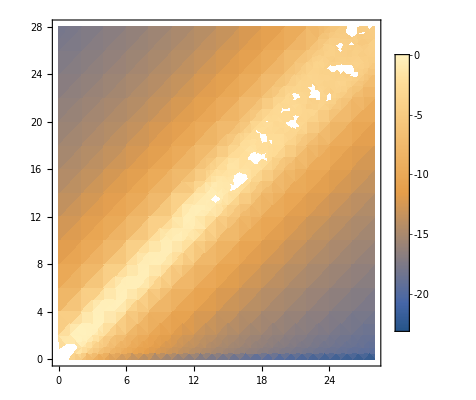

```mathematica
Series[Ζtest[a,uν],{a,0,14}];
smalla=%//Normal;
(largea/.a->(u+z))-(smalla/.a->(u-z))//Simplify;
Series[%,{uν,0,1}]//PowerExpand//Normal//Simplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1/z)],{u,0,28},{z,0,28},PlotLegends->Automatic,PlotRange->All]
```

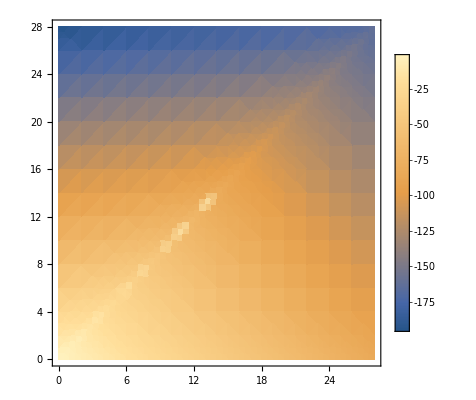

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

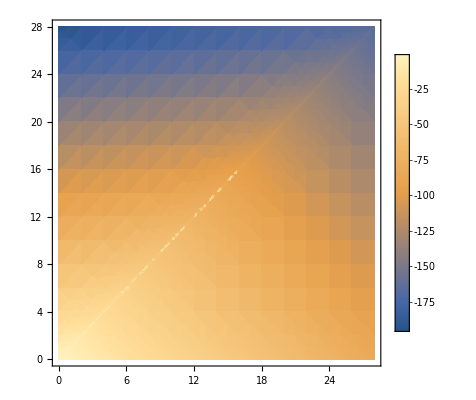

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic,MaxRecursion->4]
```

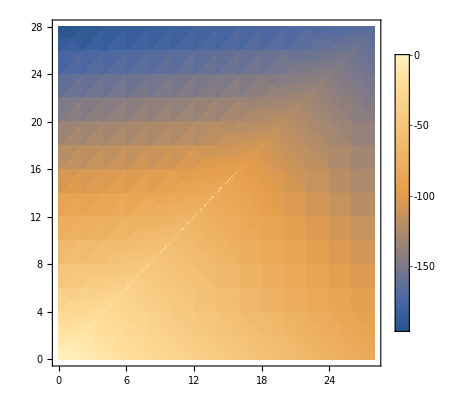

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic,MaxRecursion->5]
```

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,-5,0},PlotLegends->Automatic,MaxRecursion->5]
```

$Aborted

This plot needs to be improved, try interpolating for small u and z as well.

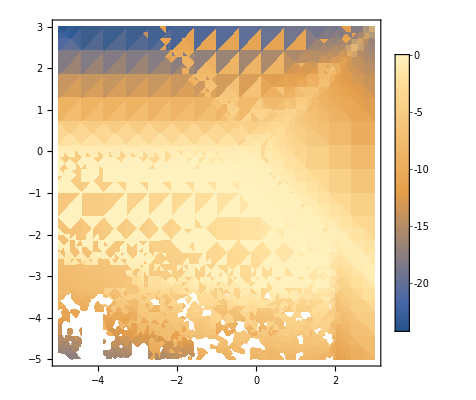

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,3},{zt,-5,3},PlotLegends->Automatic]
```

We can see the plasmon line! (u is along the bottom of the plot, compare to notes)

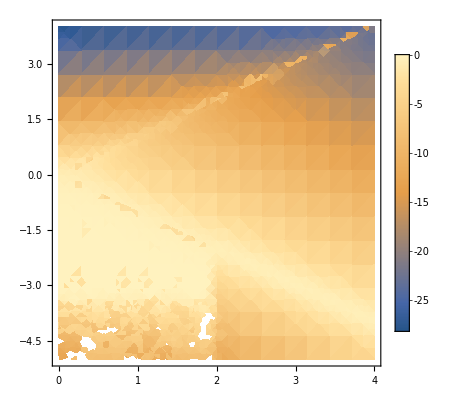

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,4},{zt,-5,4},PlotLegends->Automatic]
```

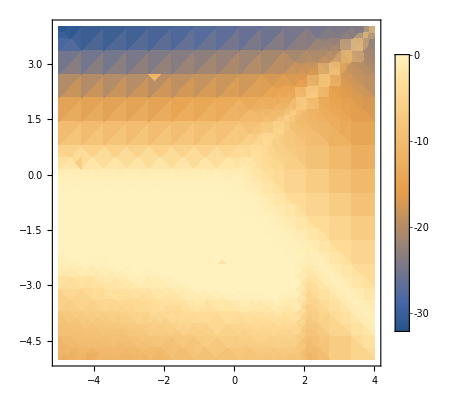

```mathematica
DensityPlot[Log10@Abs@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,4},{zt,-5,4},PlotLegends->Automatic]
```

Using Abs sign w in Ζ-Ζ

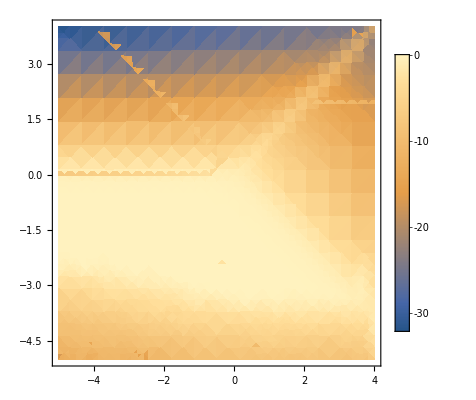

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,4},{zt,-5,4},PlotLegends->Automatic]
```

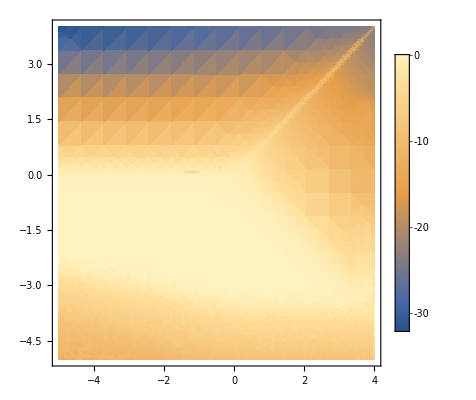

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,4},{zt,-5,4},PlotLegends->Automatic,MaxRecursion->4]
```

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,5},{zt,-5,5},PlotLegends->Automatic,MaxRecursion->4]
```

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,5},{zt,-5,5},PlotLegends->Automatic,MaxRecursion->4]
```

-Graphics-

```mathematica
1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.up->u
DensityPlot[Log10@Abs@Im[-1/N[%/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,5},{zt,-5,5},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"Im[-1/ϵ_M](u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

1+((u+ⅈ uν) (1/(4 z^3)ⅈ χ^2 (-1/2 (1+uν^2-(u-z)^2) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+1/2 (1+uν^2-(u+z)^2) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])+1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])))/(u+1/(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))ⅈ uν z^2 (1/(4 z^3)ⅈ χ^2 (-1/2 (1+uν^2-(u-z)^2) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+1/2 (1+uν^2-(u+z)^2) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])+1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])))

-Graphics-

```mathematica
Plot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt}/.zt->-4,{ut,-5,4},PlotLegends->Automatic]
```

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,0,4},{zt,-5,4},PlotLegends->Automatic]
```

```mathematica
Ζtest[a,uν]
```

{a+a uν (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)],uν+1/2 (1-a^2+uν^2) (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])-1/2 a uν Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)]}

```mathematica
Series[Ζtest[a,uν],{a,0,12}]//Simplify
largea=%//Normal
(%/.a->(u+z))-(%/.a->(u-z))//FullSimplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1)]/.{u->10^ut,z->10^zt},{ut,-5,0},{zt,-5,0},PlotLegends->Automatic](*0th moment*)
```

{(2-2 uν ArcTan[1/uν]) a-(2 a^3)/(3 (1+uν^2)^2)+(2 (-1+5 uν^2) a^5)/(15 (1+uν^2)^4)-(2 (3-42 uν^2+35 uν^4) a^7)/(105 (1+uν^2)^6)+(2 (-1+27 uν^2-63 uν^4+21 uν^6) a^9)/(63 (1+uν^2)^8)-(2 (5-220 uν^2+990 uν^4-924 uν^6+165 uν^8) a^11)/(495 (1+uν^2)^10)+O[a]^13,(uν-(1+uν^2) ArcTan[1/uν])+(-uν/(1+uν^2)+ArcTan[1/uν]) a^2-(2 uν a^4)/(3 (1+uν^2)^3)+(2 uν (-3+5 uν^2) a^6)/(15 (1+uν^2)^5)-(2 (uν (3-14 uν^2+7 uν^4)) a^8)/(21 (1+uν^2)^7)+(2 uν (-5+45 uν^2-63 uν^4+15 uν^6) a^10)/(45 (1+uν^2)^9)-(2 (uν (15-220 uν^2+594 uν^4-396 uν^6+55 uν^8)) a^12)/(165 (1+uν^2)^11)+O[a]^13}

{-(2 a^3)/(3 (1+uν^2)^2)+(2 a^5 (-1+5 uν^2))/(15 (1+uν^2)^4)-(2 a^7 (3-42 uν^2+35 uν^4))/(105 (1+uν^2)^6)+(2 a^9 (-1+27 uν^2-63 uν^4+21 uν^6))/(63 (1+uν^2)^8)-(2 a^11 (5-220 uν^2+990 uν^4-924 uν^6+165 uν^8))/(495 (1+uν^2)^10)+a (2-2 uν ArcTan[1/uν]),uν-(2 a^4 uν)/(3 (1+uν^2)^3)+(2 a^6 uν (-3+5 uν^2))/(15 (1+uν^2)^5)-(2 a^8 uν (3-14 uν^2+7 uν^4))/(21 (1+uν^2)^7)+(2 a^10 uν (-5+45 uν^2-63 uν^4+15 uν^6))/(45 (1+uν^2)^9)-(2 a^12 uν (15-220 uν^2+594 uν^4-396 uν^6+55 uν^8))/(165 (1+uν^2)^11)-(1+uν^2) ArcTan[1/uν]+a^2 (-uν/(1+uν^2)+ArcTan[1/uν])}

{(2 (-3465 (u-z)+(1155 (u-z)^3)/((1+uν^2)^2)-(231 (-1+5 uν^2) (u-z)^5)/((1+uν^2)^4)+(33 (3-42 uν^2+35 uν^4) (u-z)^7)/((1+uν^2)^6)-(55 (-1+3 uν^2 (9+7 uν^2 (-3+uν^2))) (u-z)^9)/((1+uν^2)^8)+(7 (5+11 uν^2 (-20+90 uν^2-84 uν^4+15 uν^6)) (u-z)^11)/((1+uν^2)^10)+3465 (u+z)-(1155 (u+z)^3)/((1+uν^2)^2)+(231 (-1+5 uν^2) (u+z)^5)/((1+uν^2)^4)-(33 (3-42 uν^2+35 uν^4) (u+z)^7)/((1+uν^2)^6)+(55 (-1+3 uν^2 (9+7 uν^2 (-3+uν^2))) (u+z)^9)/((1+uν^2)^8)-(7 (5+11 uν^2 (-20+90 uν^2-84 uν^4+15 uν^6)) (u+z)^11)/((1+uν^2)^10)-6930 uν z ArcCot[uν]))/3465,1/(3465 (1+uν^2)^11)(3465 uν (1+uν^2)^10 (u-z)^2+2310 uν (1+uν^2)^8 (u-z)^4+462 uν (3-5 uν^2) (1+uν^2)^6 (u-z)^6+330 uν (1+uν^2)^4 (3+7 uν^2 (-2+uν^2)) (u-z)^8+154 uν (1+uν^2)^2 (5-45 uν^2+63 uν^4-15 uν^6) (u-z)^10+42 uν (15+11 uν^2 (-20+54 uν^2-36 uν^4+5 uν^6)) (u-z)^12-3465 uν (1+uν^2)^10 (u+z)^2-2310 uν (1+uν^2)^8 (u+z)^4+462 uν (1+uν^2)^6 (-3+5 uν^2) (u+z)^6-330 uν (1+uν^2)^4 (3+7 uν^2 (-2+uν^2)) (u+z)^8+154 uν (1+uν^2)^2 (-5+45 uν^2-63 uν^4+15 uν^6) (u+z)^10-42 uν (15+11 uν^2 (-20+54 uν^2-36 uν^4+5 uν^6)) (u+z)^12+13860 u (1+uν^2)^11 z ArcCot[uν])}

-Graphics-

```mathematica
Series[Ζtest[a,uν],{a,1,8}]//Simplify
largea=%//Normal
(%/.a->(u+z))-(%/.a->(u-z))//Simplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1)]/.{u->10^ut,z->10^zt},{ut,0,4},{zt,-5,4},PlotLegends->Automatic](*0th moment*)
```

{(1-uν ArcTan[2/uν]+1/4 uν^2 Log[1+4/uν^2])+(2-uν ArcTan[2/uν]-1/2 Log[1+4/uν^2]) (a-1)+(1/(4+uν^2)-1/4 Log[1+4/uν^2]) (a-1)^2-(2 (-4+uν^2) (a-1)^3)/(3 (uν^2 (4+uν^2)^2))+(2 (4+5 uν^2) (a-1)^4)/(3 uν^2 (4+uν^2)^3)+(2 (-96-96 uν^2-46 uν^4+5 uν^6) (a-1)^5)/(15 uν^4 (4+uν^2)^4)-(2 (64+80 uν^2+28 uν^4+35 uν^6) (a-1)^6)/(15 (uν^4 (4+uν^2)^5))+(2 (5120+7680 uν^2+4800 uν^4+1488 uν^6+672 uν^8-35 uν^10) (a-1)^7)/(105 uν^6 (4+uν^2)^6)+(2 (512+896 uν^2+672 uν^4+312 uν^6-84 uν^8+63 uν^10) (a-1)^8)/(21 uν^6 (4+uν^2)^7)+O[a-1]^9,-1/2 uν (-2+uν ArcTan[2/uν]+Log[1+4/uν^2])+(ArcTan[2/uν]-1/2 uν Log[1+4/uν^2]) (a-1)+(-(2+uν^2)/(4 uν+uν^3)+1/2 ArcTan[2/uν]) (a-1)^2-(8 (a-1)^3)/(3 (uν (4+uν^2)^2))-(2 (-8-6 uν^2+uν^4) (a-1)^4)/(3 (uν^3 (4+uν^2)^3))+(4 (16+16 uν^2+15 uν^4) (a-1)^5)/(15 uν^3 (4+uν^2)^4)+(2 (-256-320 uν^2-160 uν^4-68 uν^6+5 uν^8) (a-1)^6)/(15 uν^5 (4+uν^2)^5)-(16 (128+192 uν^2+120 uν^4+35 uν^8) (a-1)^7)/(105 (uν^5 (4+uν^2)^6))+((6144+10752 uν^2+8064 uν^4+3360 uν^6+624 uν^8+364 uν^10-14 uν^12) (a-1)^8)/(21 uν^7 (4+uν^2)^7)+O[a-1]^9}

{1-(2 (-1+a)^3 (-4+uν^2))/(3 uν^2 (4+uν^2)^2)+(2 (-1+a)^4 (4+5 uν^2))/(3 uν^2 (4+uν^2)^3)+(2 (-1+a)^5 (-96-96 uν^2-46 uν^4+5 uν^6))/(15 uν^4 (4+uν^2)^4)-(2 (-1+a)^6 (64+80 uν^2+28 uν^4+35 uν^6))/(15 uν^4 (4+uν^2)^5)+(2 (-1+a)^7 (5120+7680 uν^2+4800 uν^4+1488 uν^6+672 uν^8-35 uν^10))/(105 uν^6 (4+uν^2)^6)+(2 (-1+a)^8 (512+896 uν^2+672 uν^4+312 uν^6-84 uν^8+63 uν^10))/(21 uν^6 (4+uν^2)^7)-uν ArcTan[2/uν]+(-1+a) (2-uν ArcTan[2/uν]-1/2 Log[1+4/uν^2])+(-1+a)^2 (1/(4+uν^2)-1/4 Log[1+4/uν^2])+1/4 uν^2 Log[1+4/uν^2],-(8 (-1+a)^3)/(3 uν (4+uν^2)^2)-(2 (-1+a)^4 (-8-6 uν^2+uν^4))/(3 uν^3 (4+uν^2)^3)+(4 (-1+a)^5 (16+16 uν^2+15 uν^4))/(15 uν^3 (4+uν^2)^4)+(2 (-1+a)^6 (-256-320 uν^2-160 uν^4-68 uν^6+5 uν^8))/(15 uν^5 (4+uν^2)^5)-(16 (-1+a)^7 (128+192 uν^2+120 uν^4+35 uν^8))/(105 uν^5 (4+uν^2)^6)+((-1+a)^8 (6144+10752 uν^2+8064 uν^4+3360 uν^6+624 uν^8+364 uν^10-14 uν^12))/(21 uν^7 (4+uν^2)^7)+(-1+a)^2 (-(2+uν^2)/(4 uν+uν^3)+1/2 ArcTan[2/uν])-1/2 uν (-2+uν ArcTan[2/uν]+Log[1+4/uν^2])+(-1+a) (ArcTan[2/uν]-1/2 uν Log[1+4/uν^2])}

{1/105 ((70 (-4+uν^2) (-1+u-z)^3)/(uν^2 (4+uν^2)^2)-(14 (-96-96 uν^2-46 uν^4+5 uν^6) (-1+u-z)^5)/(uν^4 (4+uν^2)^4)-(2 (5120+7680 uν^2+4800 uν^4+1488 uν^6+672 uν^8-35 uν^10) (-1+u-z)^7)/(uν^6 (4+uν^2)^6)-(70 (4+5 uν^2) (1-u+z)^4)/(uν^2 (4+uν^2)^3)+(14 (64+80 uν^2+28 uν^4+35 uν^6) (1-u+z)^6)/(uν^4 (4+uν^2)^5)-(10 (512+896 uν^2+672 uν^4+312 uν^6-84 uν^8+63 uν^10) (1-u+z)^8)/(uν^6 (4+uν^2)^7)-(70 (-4+uν^2) (-1+u+z)^3)/(uν^2 (4+uν^2)^2)+(70 (4+5 uν^2) (-1+u+z)^4)/(uν^2 (4+uν^2)^3)+(14 (-96-96 uν^2-46 uν^4+5 uν^6) (-1+u+z)^5)/(uν^4 (4+uν^2)^4)-(14 (64+80 uν^2+28 uν^4+35 uν^6) (-1+u+z)^6)/(uν^4 (4+uν^2)^5)+(2 (5120+7680 uν^2+4800 uν^4+1488 uν^6+672 uν^8-35 uν^10) (-1+u+z)^7)/(uν^6 (4+uν^2)^6)+(10 (512+896 uν^2+672 uν^4+312 uν^6-84 uν^8+63 uν^10) (-1+u+z)^8)/(uν^6 (4+uν^2)^7)-105 (1-u+z)^2 (1/(4+uν^2)-1/4 Log[1+4/uν^2])+105 (-1+u+z)^2 (1/(4+uν^2)-1/4 Log[1+4/uν^2])+105/2 (-1+u-z) (-4+2 uν ArcTan[2/uν]+Log[1+4/uν^2])-105/2 (-1+u+z) (-4+2 uν ArcTan[2/uν]+Log[1+4/uν^2])),1/105 ((280 (-1+u-z)^3)/(uν (4+uν^2)^2)-(28 (16+16 uν^2+15 uν^4) (-1+u-z)^5)/(uν^3 (4+uν^2)^4)+(16 (128+192 uν^2+120 uν^4+35 uν^8) (-1+u-z)^7)/(uν^5 (4+uν^2)^6)+(70 (-8-6 uν^2+uν^4) (1-u+z)^4)/(uν^3 (4+uν^2)^3)-(14 (-256-320 uν^2-160 uν^4-68 uν^6+5 uν^8) (1-u+z)^6)/(uν^5 (4+uν^2)^5)-(5 (6144+10752 uν^2+8064 uν^4+3360 uν^6+624 uν^8+364 uν^10-14 uν^12) (1-u+z)^8)/(uν^7 (4+uν^2)^7)-(280 (-1+u+z)^3)/(uν (4+uν^2)^2)-(70 (-8-6 uν^2+uν^4) (-1+u+z)^4)/(uν^3 (4+uν^2)^3)+(28 (16+16 uν^2+15 uν^4) (-1+u+z)^5)/(uν^3 (4+uν^2)^4)+(14 (-256-320 uν^2-160 uν^4-68 uν^6+5 uν^8) (-1+u+z)^6)/(uν^5 (4+uν^2)^5)-(16 (128+192 uν^2+120 uν^4+35 uν^8) (-1+u+z)^7)/(uν^5 (4+uν^2)^6)+(5 (6144+10752 uν^2+8064 uν^4+3360 uν^6+624 uν^8+364 uν^10-14 uν^12) (-1+u+z)^8)/(uν^7 (4+uν^2)^7)-105 (1-u+z)^2 (-(2+uν^2)/(4 uν+uν^3)+1/2 ArcTan[2/uν])+105 (-1+u+z)^2 (-(2+uν^2)/(4 uν+uν^3)+1/2 ArcTan[2/uν])-105 (-1+u-z) (ArcTan[2/uν]-1/2 uν Log[1+4/uν^2])+105 (-1+u+z) (ArcTan[2/uν]-1/2 uν Log[1+4/uν^2]))}

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/(ϵM[u,z,uν]/.uν->1/z/."χ"->1)]/.{u->10^ut,z->10^zt},{ut,0,28},{zt,0,28},PlotLegends->Automatic]
```

-Graphics-

```mathematica
True&&True&&False
```

False

```mathematica
Series[Ζtest[a,uν],{a,0,2}]
smalla=%//Normal
(largea/.a->(u+z))-(smalla/.a->(u-z))//Simplify
DensityPlot[Log10@Im[-1/({1,I}.%/.uν->1)]/.u->z+ϵ,{ϵ,-3,3},{z,0,28},PlotLegends->Automatic]
```

{(2-2 uν ArcTan[1/uν]) a+O[a]^3,(uν-(1+uν^2) ArcTan[1/uν])+((-uν+ArcTan[1/uν]+uν^2 ArcTan[1/uν]) a^2)/(1+uν^2)+O[a]^3}

{a (2-2 uν ArcTan[1/uν]),uν-(1+uν^2) ArcTan[1/uν]+(a^2 (-uν+ArcTan[1/uν]+uν^2 ArcTan[1/uν]))/(1+uν^2)}

{2/(3 (u+z))+2 (u-z) (-1+uν ArcTan[1/uν]),-uν+(uν (u-z)^2)/(1+uν^2)-(2 uν)/(3 (u+z)^2)+(1+uν^2) ArcTan[1/uν]-(u-z)^2 ArcTan[1/uν]}

-Graphics-

```mathematica
ϵRPAC[u,z,ν/z]//Simplify
Series[%,{z,∞,4}]
```

{1+1/(16 z^5)χ^2 (8 z^3+4 (u-z) z ν (ArcTan[((1+u-z) z)/ν]+ArcTan[(z (1-u+z))/ν])+4 z (u+z) ν (ArcTan[(z (-1+u+z))/ν]-ArcTan[(z (1+u+z))/ν])-(z^2-(u-z)^2 z^2+ν^2) Log[((1+u-z)^2+ν^2/z^2)/((1-u+z)^2+ν^2/z^2)]+(z^2-z^2 (u+z)^2+ν^2) Log[((1+u+z)^2+ν^2/z^2)/((-1+u+z)^2+ν^2/z^2)]),1/(8 z^5)χ^2 ((z^2-(u-z)^2 z^2+ν^2) (ArcTan[((1+u-z) z)/ν]+ArcTan[(z (1-u+z))/ν])-(z^2-z^2 (u+z)^2+ν^2) (-ArcTan[(z (-1+u+z))/ν]+ArcTan[(z (1+u+z))/ν])+(u-z) z ν Log[((1+u-z)^2+ν^2/z^2)/((1-u+z)^2+ν^2/z^2)]-z (u+z) ν Log[((1+u+z)^2+ν^2/z^2)/((-1+u+z)^2+ν^2/z^2)])}

$Aborted

```mathematica
1/(u+z-ζ y + I ν/z)- 1/(u-z-ζ y + I ν/z)
```

-1/(u-z-y ζ+(ⅈ ν)/z)+1/(u+z-y ζ+(ⅈ ν)/z)

```mathematica
(2 z)/(u+z-ζ y + I ν/z)^2==1/(u+z-ζ y + I ν/z)- 1/(u-z-ζ y + I ν/z)//Simplify
```

(z (u z-y z ζ+ⅈ ν))/((-u z+z^2+y z ζ-ⅈ ν) (u z+z^2-y z ζ+ⅈ ν))==0

```mathematica
Integrate[(2 z)/((u+z-ζ y + I ν/z)(u-z-ζ y + I ν/z)),{y,-1,1}]
```

$Aborted

```mathematica
Integrate[(2 z ζ^2)/((u+z-ζ y + I ν/z)(u-z-ζ y + I ν/z)),{ζ,0,1}]
```

$Aborted

#### Final Comparison of Dielectric

```mathematica
1 + ((up +I uν) ({1,I} . ϵRPAC[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPAC[up,z,uν]-1)/(ϵRPA0[z]-1))/.up->u;
DensityPlot[Log10@Abs@Im[-1/N[%/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"Im[-1/ϵ_M](u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"Im[-1/ϵ_M](u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/N[ϵM[u,z,uν]/.uν->1/z/."χ"->1,50]]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->5,PlotLabel->"Im[-1/ϵ_M](u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,FeTotalparams]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_Fe(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,SiO2Totalparams]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_SiO_2(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,MgOTotalparams]/.{u->10^ut,z->10^zt},{ut,-5,28},{zt,-5,28},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_MgO(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"}]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,SiO2Totalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_MgO(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,FeTotalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_Fe(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
```

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,FeTotalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_Fe(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
DensityPlot[Log10@StructureFunctionuz[u,z,SiO2Totalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_MgO(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
DensityPlot[Log10@StructureFunctionuz[u,z,FeTotalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_Fe(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
DensityPlot[Log10@StructureFunctionuz[u,z,SiO2Totalparams]/.{u->10^ut,z->10^zt},{ut,-5,6},{zt,-5,6},PlotLegends->Automatic,MaxRecursion->4,PlotLabel->"S_MgO(u=ω/v_F,z=k/(2 SubscriptBox[k, F]))",FrameLabel->{"Log_10u","Log_10z"},PlotRange->All]
```

-Graphics-

-Graphics-